## Random circuits and circuit visualization

```mathematica
randomCircuit[Nq_,Dg_]:=Module[{circ},
circ={};
circ=Reap[
For[i=1,i≤Dg,i++,
q1=1+RandomInteger[Nq-1];
q2=1+RandomInteger[Nq-1];
If[q1==q2, q2=Mod[q2+1,Nq+1]];
If[q2==0,q2=1];
Sow[{i,Sort[{q1,q2}]}];
]
];
circ[[2,1]]
];
```

```mathematica
QBpitch=100;
Gatepitch=100;
QBy[q_]:=-(q-1) QBpitch;
Gx[g_]:=g Gatepitch;

DrawCircuit[Nq_,circ_]:=Module[{hlen, q, qblines,gatelines,gatecircles},
hlen=Gatepitch (Length[circ]+1);
qblines=Reap[
For[q=1,q≤Nq,q++,
Sow[Line[{{0,QBy[q]},{hlen,QBy[q]}}]];
];
];
qblines=qblines[[2,1]];

gatelines=Reap[
For[g=1,g≤Length[circ],g++,
Sow[Line[{{Gx[g],QBy[circ[[g,2,1]]]},{Gx[g],QBy[circ[[g,2,2]]]}}]];
Sow[Disk[{Gx[g],QBy[circ[[g,2,1]]]},Gatepitch/10]];
Sow[Disk[{Gx[g],QBy[circ[[g,2,2]]]},Gatepitch/10]];
Sow[Text[ToString[circ[[g,1]]],{Gx[g]-Gatepitch/4,QBy[circ[[g,2,1]]]-Gatepitch/4}]];
];
];
gatelines=gatelines[[2,1]];

(*gatecircles=Reap[
For[g=1,g≤Length[circ],g++,
Sow[Disk[{Gx[g],QBy[circ[[g,2,1]]]},Gatepitch/10]];
Sow[Disk[{Gx[g],QBy[circ[[g,2,2]]]},Gatepitch/10]];
];
];*)

ret=Join[qblines,gatelines];
ret
];
```

{{1,{4,6}},{2,{5,10}},{3,{4,8}},{4,{3,8}},{5,{1,4}},{6,{7,8}},{7,{1,3}},{8,{1,9}},{9,{2,8}},{10,{5,8}},{11,{5,8}},{12,{2,8}},{13,{4,10}},{14,{2,10}},{15,{3,4}},{16,{3,9}},{17,{2,6}},{18,{7,9}},{19,{3,7}},{20,{9,10}}}

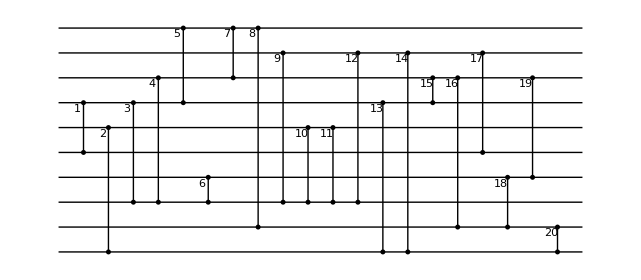

```mathematica
Nq=10;
Dg=20;
circ=randomCircuit[Nq,Dg]
cg=DrawCircuit[Nq,circ];
Graphics[cg]
```

```mathematica
LayerCircuit[Nq_,circ_]:=Module[{g, layeredCirc,layer,blockTbl,gUsedTbl},

layeredCirc=Reap[
gUsedTbl=Table[0,Length[circ]];
While[Total[gUsedTbl ]≠ Length[circ],
layer=Reap[
g=1;
blockTbl=Table[0,Nq];
While[Total[blockTbl ]≠ Nq && g≤ Length[circ],
{
If[gUsedTbl[[g]]==0,
{
q1=circ[[g,2,1]];
q2=circ[[g,2,2]];
If[blockTbl[[q1]]==0 && blockTbl[[q2]]==0,
{
Sow[circ[[g]]];
gUsedTbl[[g]]=1;
}
];
blockTbl[[q1]]=1;
blockTbl[[q2]]=1;
}];
g++;
}];
]; (*Reap layer*)
layer=layer[[2,1]];
Sow[layer];
];
]; (*Circuit reap*)
layeredCirc=layeredCirc[[2,1]];
layeredCirc
];
```

```mathematica
layeredCirc=LayerCircuit[Nq,circ]
```

{{{1,{4,6}},{2,{5,10}}},{{3,{4,8}}},{{4,{3,8}},{5,{1,4}}},{{6,{7,8}},{7,{1,3}},{13,{4,10}}},{{8,{1,9}},{9,{2,8}},{15,{3,4}}},{{10,{5,8}},{16,{3,9}}},{{11,{5,8}},{18,{7,9}}},{{12,{2,8}},{19,{3,7}}},{{14,{2,10}}},{{17,{2,6}},{20,{9,10}}}}

```mathematica
QBpitch=100;
Gatelpitch=20;
Layerpitch=100;
Gxl[g_,o_]:=o+g Gatelpitch;

DrawLayeredCircuit[Nq_,circ_]:=Module[{l,circl,hlen, q, qblines,gatelines,offset,offsetx},

offset=Layerpitch/2;
gatelines=Reap[
For[l=1,l≤Length[circ],l++,
circl=circ[[l]];
offsetx=0;
For[g=1,g≤Length[circl],g++,
q1=circl[[g,2,1]];
q2=circl[[g,2,2]];
Sow[Line[{{Gxl[g,offset],QBy[q1]},{Gxl[g,offset],QBy[q2]}}]];
Sow[Disk[{Gxl[g,offset],QBy[q1]},Gatepitch/10]];
Sow[Disk[{Gxl[g,offset],QBy[q2]},Gatepitch/10]];
Sow[Text[ToString[circl[[g,1]]],{Gxl[g,offset]-Gatepitch/4,QBy[q1]-Gatepitch/4}]];
offsetx+=Gatelpitch;
];
offset+=offsetx;
If[l≠Length[circ],
Sow[{Dashed,Line[{{offset+Layerpitch/2,0},{offset+Layerpitch/2,-(Nq-1) QBpitch}}]}];
offset+=Layerpitch;
];];
];
gatelines=gatelines[[2,1]];
offset+=Layerpitch/2;

qblines=Reap[
For[q=1,q≤Nq,q++,
Sow[Line[{{0,QBy[q]},{offset,QBy[q]}}]];
];
];
qblines=qblines[[2,1]];


ret=Join[qblines,gatelines];
ret
];
```

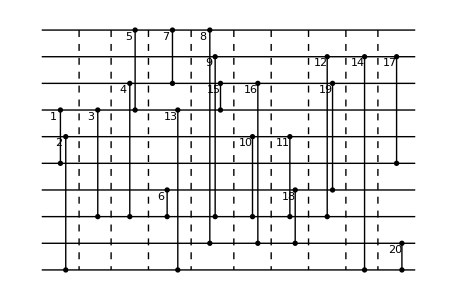

```mathematica
cg=DrawLayeredCircuit[Nq,layeredCirc];
Graphics[cg]
```

## Block aggregation

```mathematica
EvaluateGateCoverage[S_,G_,Nq_,Qmax_,Mmax_]:=Module[{gateCoverage,qubitNonCoverage,m,n},
gateCoverage=0;
qubitNonCoverage=0;
m=1;
For[n=1,n≤Length[S],n++,
(*If set size exceed processing zone size, add size to non covered qubit count*)
If[Length[S[[n]]]>Qmax,{
qubitNonCoverage+=Length[S[[n]]];
}];
(*For the Mmax largest sets not exceeding processing zone size, add gate cover set size to gate coverage count*)
If[Length[S[[n]]]≤Qmax && m≤Mmax,{
gateCoverage+=Length[G[[n]]];
m+=1;
}];
];
{gateCoverage,qubitNonCoverage}
];

AggregateBlocksStep[layeredCirc_,Nq_,Qmax_,Mmax_]:=Module[{S,G,Sbest,Gbest,ctbl,Sp,Gp,l,r,g,n,m,cn,cm,j,k,temp,echo,ck,gateCoverage,qubitNonCoverage,bestGateCoverage,gateCoverageTbl,bestGateCoverageTbl,qubitNonCoverageTbl,zoneCtr},
S=Table[{n},{n,1,Nq}]; (*qubit sets*)
Sbest={};
G=Table[{},Nq]; (*gate coverage sets*)
Gbest={};
ctbl=Table[n,{n,1,Nq}]; (*pointer variables*)
bestGateCoverage=0;
gateCoverageTbl={};
qubitNonCoverageTbl={};
bestGateCoverageTbl={};

For[l=1,l≤Length[layeredCirc],l++,
For[r=1,r≤Length[layeredCirc[[l]]],r++,

g=layeredCirc[[l,r]];
n=g[[2,1]]; (*QB index of 1st gate QB*)
m=g[[2,2]]; (*QB index of 2nd gate QB*)
cn=ctbl[[n]]; (*set index of 1st gate QB*)
cm=ctbl[[m]]; (*set index of 2nd gate QB*)
G[[cn]]=Append[G[[cn]],g]; (*Merge gate g to gate coverage set of qubit n*)
If[cn==cm,Continue[]];
(*If size of QB set cm exceeds set cn, swap cn and cm -> always merge smaller to larger set*)
If[Length[S[[cm]]]>Length[S[[cn]]],{temp=cn; cn=cm,cm=temp}];
S[[cn]]=Join[S[[cn]],S[[cm]]]; (*Merge qubit set cm to qubit set cn*)
G[[cn]]=Join[G[[cn]],G[[cm]]]; (*Merge gate coverage set cm to gate coverage set cn*)
For[j=1,j≤Length[S[[cm]]],j++,ctbl[[S[[cm,j]]]]=cn]; (*reroute pointers of all qubits in set cm to set cn*)
S[[cm]]={}; (*discard qubit set cm*)
G[[cm]]={}; (*discard qubit set cn*)
(*Keep S and G sorted by size in decreasing order*)
If[cn>1,{
While[Length[S[[cn]]]>Length[S[[cn-1]]],{
If[cn==1,Break[]];
For[k=1,k≤Length[S[[cn]]],k++,ctbl[[S[[cn,k]]]]=cn-1];
For[k=1,k≤Length[S[[cn-1]]],k++,ctbl[[S[[cn-1,k]]]]=cn];
S[[{cn,cn-1}]]=S[[{cn-1,cn}]];
G[[{cn,cn-1}]]=G[[{cn-1,cn}]];
cn=cn-1;
}];
}];
If[cm<Nq,{
While[0<Length[S[[cm+1]]],{
For[k=1,k≤Length[S[[cm+1]]],k++,ctbl[[S[[cm+1,k]]]]=cm];
S[[cm]]=S[[cm+1]];
S[[cm+1]]={};
G[[cm]]=G[[cm+1]];
G[[cm+1]]={};
cm=cm+1;
If[cm≥Length[S],Break[]];
}];
}];

(*evaluate gate coverage of updated sets*)
{gateCoverage,qubitNonCoverage}=EvaluateGateCoverage[S,G,Nq,Qmax,Mmax];

(*Termination condition: If the number of qubits in all sets of size less than processing zone is less than Mmax * Qmax, theres not enough qubits left to fully populate the processing zones - terminate the aggregation*)
If[Nq-qubitNonCoverage <Mmax Qmax,Return[{Sbest,Gbest,gateCoverageTbl,bestGateCoverageTbl,qubitNonCoverageTbl},Module]];

(*compute number of gates covered by Mmax largest sets of size <Q*)
zoneCtr=1;
gateCoverage=0;
For[ck=1,ck≤Length[G],ck++,
If[Length[S[[ck]]]≤Qmax && zoneCtr≤Mmax, {gateCoverage+=Length[G[[ck]]],zoneCtr++}];
];
(*If gate coverage exceed best previous value, update best values and sets*)
If[gateCoverage>bestGateCoverage,{
bestGateCoverage=gateCoverage;
Sbest=S;
Gbest=G;
}];
(*diagnostics output*)
gateCoverageTbl=Append[gateCoverageTbl,gateCoverage];
bestGateCoverageTbl=Append[bestGateCoverageTbl,bestGateCoverage];
qubitNonCoverageTbl=Append[qubitNonCoverageTbl,qubitNonCoverage];
]; (*for r*)
]; (*for l*)

(*If no termination occurred during aggregation, return here*)
Return[{Sbest,Gbest,gateCoverageTbl,bestGateCoverageTbl,qubitNonCoverageTbl}]
];
```

{{{4,6,8,3},{5,10},{1},{2},{7},{9},{},{},{},{}},{{{1,{4,6}},{3,{4,8}},{4,{3,8}}},{{2,{5,10}}},{},{},{},{},{},{},{},{}},{1,1,2,3,1,1},{1,1,2,3,3,3},{0,0,0,0,5,6}}

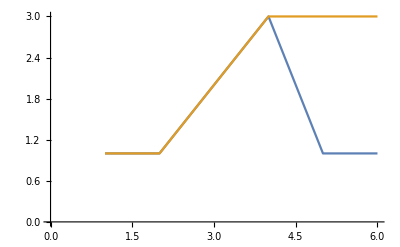

```mathematica
Qmax=4;
Mmax=1;
{Sbest,Gbest,gateCoverageTbl,bestGateCoverageTbl,qubitNonCoverageTbl}=AggregateBlocksStep[layeredCirc,Nq,Qmax,Mmax]
ListPlot[{gateCoverageTbl,bestGateCoverageTbl},Joined->True]
```

```mathematica
AggregateBlocksStepPostProcess[S_,G_,Nq_,Qmax_,Mmax_]:=Module[{SP,GP,Iset,c,m,n,k,qi,q,SPi},
SP={};
GP={};
Iset={};
c=Table[0,Nq];
m=1;

(*Take Mmax largest subsets of S to be to processing zone sets, add all remaining QB to idle pool*)
For[n=1,n≤Length[S],n++,
If[Length[S[[n]]]≤Qmax && m≤Mmax,{
SP=Append[SP,S[[n]]];
GP=Append[GP,G[[n]]];
k=1;
For[qi=1,qi≤Length[S[[n]]],qi++,
q=S[[n,qi]];
c[[q]]={"p",m,k,"a"};
k++;
];
m++;
},{
Iset=Join[Iset,S[[n]]]
}];
];

(*Pad all processing zone sets with size < Qmax with QB from idle pool. Put these in separate idle subsets and remove from global idle pool*) 
For[m=1,m≤Mmax,m++,
SPi={};
(*quick fix: if there is only on active QB in proc zone m, turn this into an idle QB*)
If[Length[SP[[m]]]==1,{
q=SP[[m,1]];
SP[[m]]={};
SPi={q};
c[[q]]={"p",m,1,"i"};
}];
k=Length[SP[[m]]]+Length[SPi]+1;
While[Length[SP[[m]]]+Length[SPi] < Qmax,
q=Iset[[1]];
SPi=Append[SPi,q];
c[[q]]={"p",m,k,"i"};
Iset=Drop[Iset,1];
k++;
];
SP[[m]]={SP[[m]],SPi};
];

(*Assign pointer variable for all QB remaining in global idle pool*)
For[qi=1,qi≤Length[Iset],qi++,
q=Iset[[qi]];
c[[q]]={"i",1,qi,"i"};
];

{SP,GP,Iset,c}
];


(*This module places idle QB from a global pool into idle storage zone with max capacities specified by Fsizes. This is a stupid first version, which just starts to place the QB from the middle to outwards. A more clever version would use some form of look-ahead, placing idle QB to be used in the next block in processing zones next to these*) 
PlaceIdlePoolQB[Fsizes_,Iset_,c_]:=Module[{Fset,numF,Isetnew,cnew,f,q,fp,fm},

numF=Length[Fsizes]; (*number of idle zones*)
f=Floor[numF/2]; (*first idle zone to be filled up*)
Fset=Table[{},numF]; (*initialize empty idle zones*)
Isetnew=Iset;
cnew=c; (*new pointer table*)

(*Fill idle zones around starting zone, 1QB right, 1QB left, move ahead once a zone is full*)
fm=f;
fp=f+1;
ctr=1;

While[Length[Isetnew]>0,{

(*right zone, first check if size exceeded*)
If[fp≤numF,
If[Length[Fset[[fp]]]>=Fsizes[[fp]],fp++]];
If[fp≤numF,
If[ Length[Fset[[fp]]]<Fsizes[[fp]],{
q=Isetnew[[1]];
Fset[[fp]]=Append[Fset[[fp]],q];
cnew[[q]]={"i",fp,Length[Fset[[fp]]],"i"};
Isetnew=DeleteCases[Isetnew,q];
}];
];
If[Length[Isetnew]==0,Return[{Fset,cnew},Module]];

(*left zone, first check if size exceeded*)
If[fm≥1,
If[Length[Fset[[fm]]]>=Fsizes[[fm]],fm--]];
If[fm>0 ,
If[Length[Fset[[fm]]]<Fsizes[[fm]],{
q=Isetnew[[1]];
Fset[[fm]]=Append[Fset[[fm]],q];
cnew[[q]]={"i",fm,Length[Fset[[fm]]],"i"};
Isetnew=DeleteCases[Isetnew,q];
}];
];
(*If all idle zones full and idle qubits left over, drop error message, exit*)
If[fp==numF && Length[Fset[[fp]]]>=Fsizes[[fp]] && fm==1 && Length[Fset[[fm]]]>=Fsizes[[fm]] &&  Length[Isetnew]>0,{
Print["Error in PlaceIdlePoolQB: No more idle zones left, not all idle QB placed!"];
Return[{Fset,cnew},Module];
}];
}];

{Fset,cnew}
];
```

```mathematica
{SP,GP,Iset,c}=AggregateBlocksStepPostProcess[Sbest,Gbest,Nq,Qmax,Mmax];
Print["SP: ",SP];
Print["GP: ",GP];
Print["Iset: ",Iset];
Print["c: ",c];

Fsizes={10,10};
{FP,cnew}=PlaceIdlePoolQB[Fsizes,Iset,c];
Print["FP: ",FP];
Print["cnew: ",cnew];
```

SP: {{{4,6,8,3},{}}}

GP: {{{1,{4,6}},{3,{4,8}},{4,{3,8}}}}

Iset: {5,10,1,2,7,9}

c: {{i,1,3,i},{i,1,4,i},{p,1,4,a},{p,1,1,a},{i,1,1,i},{p,1,2,a},{i,1,5,i},{p,1,3,a},{i,1,6,i},{i,1,2,i}}

FP: {{10,2,9},{5,1,7}}

cnew: {{i,2,2,i},{i,1,2,i},{p,1,4,a},{p,1,1,a},{i,2,1,i},{p,1,2,a},{i,2,3,i},{p,1,3,a},{i,1,3,i},{i,1,1,i}}

BlockProcessCircuit returns a data structure containing a sequence of arrangement blocks B = [B1, B2, .. Bn}
Each arrangement block Bi = {SP, GP, FP, c} contains the following information :
    SP = {{Sa1, Si1}, {Sa2, Si2}, ...} contains the qubit indices of the qubits contained in each processing zone,
where Saj contains the indices of the active qubits and Sij contains the indices of the idle qubits stored in the same zone. Either list can be empty. 
   GP = {{gi, {qi1, qi2, ..}}, ...} contains the information about the gates covered in each arrangement block. gi is a gate identifier and the list {qi1, ....} contains the indices of the qubits participating in gate gi.
    FP = {{q1_ 1, q2_ 2, ...}, ...} contains the qubits stored in the idle zones
c = {{s1, z1, k1, s2} contains the storage information for each qubit, always in order by the qubit indices. s1 = "p" or "i" tells wheter the qubit is stored in a processing or idle zone, z1 is the zone index - not unique, we use separate numbering for processing and idle zones. k1 is the qubit position within its storage zone. s2 = "a" or "i" tells whether the qubit is active or idle. qubits stored in idle zones always have s2 = "i".

```mathematica
BlockProcessCircuit[CrawInp_,Nq_,Fsizes_,Qmax_,Mmax_]:=Module[{Craw,C,B,Sbest,Gbest,gateCoverageTbl,bestGateCoverageTbl,qubitNonCoverageTbl,SP,GP,Iset,c,cnew,FP,gpi,gi},

Craw=CrawInp;
B={};

While[Length[Craw]>0,{ 
C=LayerCircuit[Nq,Craw];
{Sbest,Gbest,gateCoverageTbl,bestGateCoverageTbl,qubitNonCoverageTbl}=AggregateBlocksStep[C,Nq,Qmax,Mmax];
{SP,GP,Iset,c}=AggregateBlocksStepPostProcess[Sbest,Gbest,Nq,Qmax,Mmax];
{FP,cnew}=PlaceIdlePoolQB[Fsizes,Iset,c];

(*Delete covered gates from raw circuit*)
For[gpi=1,gpi≤Length[GP],gpi++,
For[gi=1,gi≤Length[GP[[gpi]]],gi++,
Craw=DeleteCases[Craw,GP[[gpi,gi]]];
];
];
B=Append[B,{SP,GP,FP,cnew}];
}];
B
];

PrintBP[BP_]:=Module[{step},
For[step=1,step≤Length[BP],step++,
Print["step: ",step];
Print["   SP: ",BP[[step,1]]];
Print["   FP: ",BP[[step,3]]];
Print["   GP: ",BP[[step,2]]];
Print["   c: ",BP[[step,4]]];
];
];
```

```mathematica
BP=BlockProcessCircuit[circ,Nq,Fsizes,Qmax,Mmax];
PrintBP[BP]
```

step: 1

SP: {{{4,6,8,3},{}}}

FP: {{10,2,9},{5,1,7}}

GP: {{{1,{4,6}},{3,{4,8}},{4,{3,8}}}}

c: {{i,2,2,i},{i,1,2,i},{p,1,4,a},{p,1,1,a},{i,2,1,i},{p,1,2,a},{i,2,3,i},{p,1,3,a},{i,1,3,i},{i,1,1,i}}

step: 2

SP: {{{1,4,3},{5}}}

FP: {{7,2,9},{10,8,6}}

GP: {{{5,{1,4}},{7,{1,3}}}}

c: {{p,1,1,a},{i,1,2,i},{p,1,3,a},{p,1,2,a},{p,1,4,i},{i,2,3,i},{i,1,1,i},{i,2,2,i},{i,1,3,i},{i,2,1,i}}

step: 3

SP: {{{7,8,2},{5}}}

FP: {{1,3,6},{10,9,4}}

GP: {{{6,{7,8}},{9,{2,8}}}}

c: {{i,1,1,i},{p,1,3,a},{i,1,2,i},{i,2,3,i},{p,1,4,i},{i,1,3,i},{p,1,1,a},{p,1,2,a},{i,2,2,i},{i,2,1,i}}

step: 4

SP: {{{5,10,8,4},{}}}

FP: {{9,3,7},{1,2,6}}

GP: {{{2,{5,10}},{10,{5,8}},{13,{4,10}}}}

c: {{i,2,1,i},{i,2,2,i},{i,1,2,i},{p,1,4,a},{p,1,1,a},{i,2,3,i},{i,1,3,i},{p,1,3,a},{i,1,1,i},{p,1,2,a}}

step: 5

SP: {{{3,4,1,9},{}}}

FP: {{8,6,10},{5,2,7}}

GP: {{{15,{3,4}},{16,{3,9}},{8,{1,9}}}}

c: {{p,1,3,a},{i,2,2,i},{p,1,1,a},{p,1,2,a},{i,2,1,i},{i,1,2,i},{i,2,3,i},{i,1,1,i},{p,1,4,a},{i,1,3,i}}

step: 6

SP: {{{5,8,2,10},{}}}

FP: {{9,1,6},{7,3,4}}

GP: {{{11,{5,8}},{12,{2,8}},{14,{2,10}}}}

c: {{i,1,2,i},{p,1,3,a},{i,2,2,i},{i,2,3,i},{p,1,1,a},{i,1,3,i},{i,2,1,i},{p,1,2,a},{i,1,1,i},{p,1,4,a}}

step: 7

SP: {{{7,9,3,10},{}}}

FP: {{6,4,8},{2,1,5}}

GP: {{{18,{7,9}},{19,{3,7}},{20,{9,10}}}}

c: {{i,2,2,i},{i,2,1,i},{p,1,3,a},{i,1,2,i},{i,2,3,i},{i,1,1,i},{p,1,1,a},{i,1,3,i},{p,1,2,a},{p,1,4,a}}

step: 8

SP: {{{2,6},{1,3}}}

FP: {{5,8,10},{4,7,9}}

GP: {{{17,{2,6}}}}

c: {{p,1,3,i},{p,1,1,a},{p,1,4,i},{i,2,1,i},{i,1,1,i},{p,1,2,a},{i,2,2,i},{i,1,2,i},{i,2,3,i},{i,1,3,i}}

## Qubit coordinates and placement visualization

```mathematica
yQBP[q_,c_,SP_,Fsizes_,Qmax_]:=Module[{qi,numF1,s1,s2,z,k,y},
{s1,z,k,s2}=c[[q]];
If[s1=="p" ,{
y=(z-1) Qmax+Sum[Fsizes[[j]],{j,2,z}]+k;
},
If[z>1,y=(z-1) Qmax+Sum[Fsizes[[j]],{j,2,z-1}]+k,
 {
(*count QB in 1st processing zone*)
numF1=0;
For[qi=1,qi≤Length[c],qi++,If[c[[qi,1]]=="i" && c[[qi,2]]==1,numF1++]];
y=numF1-(k-1);
}];
];
If[s1=="p" || z>1,{ y=-y,y++}];
y
];

QBPpitch=20;
QBPradius=5;
DrawQBPlacement[ytbl_,c_]:=Module[{q,s1,s2,col,ret},

ret=Reap[
For[q=1,q≤Nq,q++,
s1=c[[q,1]];
s2=c[[q,4]];
col=If[s1=="p",If[s2=="a",Red,Blue],Green];
Sow[{col,Disk[{0,QBPpitch ytbl[[q]]},QBPradius]}];
Sow[Text[ToString[q],{0,QBPpitch ytbl[[q]]}]];
];
];
ret=ret[[2,1]];
ret
];
```

{{{4,6,8,3},{}}}

{{{1,{4,6}},{3,{4,8}},{4,{3,8}}}}

{{10,2,9},{5,1,7}}

{{i,2,2,i},{i,1,2,i},{p,1,4,a},{p,1,1,a},{i,2,1,i},{p,1,2,a},{i,2,3,i},{p,1,3,a},{i,1,3,i},{i,1,1,i}}

{-5,2,-3,0,-4,-1,-6,-2,1,3}

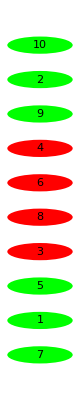

```mathematica
{SP,GP,FP,c}=BP[[1]];
SP
GP
FP
c
ytbl=Table[yQBP[q,c,SP,Fsizes,Qmax],{q,1,Nq}]
grP=DrawQBPlacement[ytbl,c];
Graphics[grP]
```

```mathematica
QBPxpitch=40;
DrawQBPlacementGlobal[BP_]:=Module[{ytbl,step,c,SP,GP,FP,q,s1,s2,col,ret},

ytbl=Table[Table[yQBP[q,BP[[step,4]],BP[[step,1]],Fsizes,Qmax],{q,1,Nq}],{step,1,Length[BP]}];

ret=Reap[
For[step=1,step≤Length[BP],step++,
{SP,GP,FP,c}=BP[[step]];

For[q=1,q≤Nq,q++,
s1=c[[q,1]];
s2=c[[q,4]];
col=If[s1=="p",If[s2=="a",Red,Blue],Green];
If[step<Length[BP],
Sow[Line[{{(step-1) QBPxpitch,QBPpitch ytbl[[step,q]]},{step  QBPxpitch,QBPpitch ytbl[[step+1,q]]}}]];
];
Sow[{col,Disk[{(step-1) QBPxpitch,QBPpitch ytbl[[step,q]]},QBPradius]}];
Sow[{Black,Circle[{(step-1) QBPxpitch,QBPpitch ytbl[[step,q]]},QBPradius]}];
Sow[Text[ToString[q],{(step-1) QBPxpitch,QBPpitch ytbl[[step,q]]}]];
];
];
];
ret=ret[[2,1]];
ret
];
```

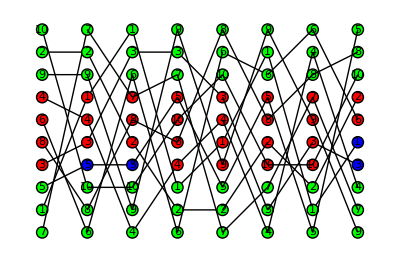

```mathematica
grP=DrawQBPlacementGlobal[BP];
Graphics[grP]
```

## Deterministic optimization

```mathematica
(*Compute sequence of Y position tables from BP data structure*)
ComputeArrangements[BP_,Nq_,Fsizes_,Qmax_,Mmax_]:=Module[{numSteps,Y,step,SP,c,q,YList},

numSteps=Length[BP];
Y={};

For[step=1,step≤numSteps,step++,
SP=BP[[step,1]];
c=BP[[step,4]];
YList=Table[0,Nq];

For[q=1,q≤Nq,q++,
YList[[q]]=yQBP[q,c,SP,Fsizes,Qmax];
];
Y=Append[Y,YList];
];
Y
];

(*compute total rearrangement cost from sequence of Y tables*)
ComputeTotalCost[Y_,Nq_]:=Module[{numSteps,step,qi,costTot,Yc,Yp,Yf},

numSteps=Length[BP];
costTot=0;
For[step=1,step<numSteps,step++,

Yc=Y[[step]];
Yf=Y[[step+1]];
For[qi=1,qi≤Nq,qi++,
costTot+=(Yc[[qi]]-Yf[[qi]])^2;
];
];
costTot
];

(*swap qubits q and q2 in step, return updated Y table for step and change of rearrangement cost function*)
UpdateStep[Y_,step_,numSteps_,q_,q2_,costTot_]:=Module[{costNew,Ynew},
costNew=costTot;
If[step>1,costNew-=(Y[[step,q]]-Y[[step-1,q]])^2+(Y[[step,q2]]-Y[[step-1,q2]])^2];
If[step<numSteps,costNew-=(Y[[step,q]]-Y[[step+1,q]])^2+(Y[[step,q2]]-Y[[step+1,q2]])^2];
Ynew=Y[[step]];
Ynew[[{q,q2}]]=Ynew[[{q2,q}]];
If[step>1,costNew+=(Ynew[[q]]-Y[[step-1,q]])^2+(Ynew[[q2]]-Y[[step-1,q2]])^2];
If[step<numSteps,costNew+=(Ynew[[q]]-Y[[step+1,q]])^2+(Ynew[[q2]]-Y[[step+1,q2]])^2];
{costNew,Ynew}
];

ImprovePlacement[BP_,Nq_,Fsizes_,Qmax_,Mmax_,echo_]:=Module[{numSteps,numF,step,z,zp,SP,GP,FP,c,SPp,GPp,FPp,cp,SPf,GPf,FPf,cf,zf,s1f,q,qi,z2,z2f,s12f,qi2,q2,s1p,z2p,s12p,k,k2,kp,k2p,SPz,SPz2,dist,distSwap,BPnew,Y,costTot,reapRes,costTotTbl,Ytemp,BPtbl},

Y=ComputeArrangements[BP,Nq,Fsizes,Qmax,Mmax];
costTot=ComputeTotalCost[Y,Nq];
If[echo==True,Print["ImprovePlacement costTot: ",costTot]];
numSteps=Length[BP];
numF=Length[Fsizes];
BPnew=BP;

reapRes=Reap[
Sow[costTot,1];
Sow[BPnew,2];
For[step=2,step≤numSteps,step++,
(*storage information from previous step*)
{SPp,GPp,FPp,cp}=BPnew[[step-1]];
If[step<Length[BP],{SPf,GPf,FPf,cf}=BPnew[[step+1]]];

(*1. - swap idle qubits between idle zones to prevent crossings*)
For[z=1,z≤numF,z++,
{SP,GP,FP,c}=BPnew[[step]];

(*iterate over all idle qubits*)
For[qi=1,qi≤Length[FP[[z]]],qi++,
{SP,GP,FP,c}=BPnew[[step]];
q=FP[[z,qi]];
zp=cp[[q,2]];
s1p=cp[[q,1]];
If[step<Length[BP], {zf=cf[[q,2]],s1f=cf[[q,1]]}];
(*if q was not idle in previous step or if it was in the same zone, we do not try to swap q*)
If[s1p!="i" || zp== z,Continue[]];

(*iterate over all idle zone QB as possible swap partners*)
For[qi2=1,qi2≤Length[FP[[zp]]],qi2++,
q2=FP[[zp,qi2]];
If[q2==q,Continue[]];
z2p=cp[[q2,2]];
s12p=cp[[q2,1]];
If[step<Length[BP], {z2f=cf[[q2,2]],s12f=cf[[q2,1]]}];

(*q2 is not a swap partner if it was not idle in previous step AND if q and q2 are contained in the same idle zone in the previous step*)
If[z2p==zp && s12p=="i",Continue[]];
(*q2 is not a swap partner if it is not idle in next step AND if q and q2 are contained in the same idle zone in the next step*)
If[step<numSteps,If[z2f==zf && s12f=="i",Continue[]]];
BPnew[[step,4,{q,q2}]]={c[[q2]],c[[q]]};
BPnew[[step,3,z]]=BPnew[[step,3,z]] /.q->q2;
BPnew[[step,3,zp]]=BPnew[[step,3,zp]] /.q2->q;
{costTot,Y[[step]]}=UpdateStep[Y,step,numSteps,q,q2,costTot];
Sow[costTot,1];
Sow[BPnew,2];
Break[];
];
];
];

(*2. - swap idle qubits within idle zones to minimize swaps*)
For[z=1,z≤numF,z++,
{SP,GP,FP,c}=BPnew[[step]];

For[qi=1,qi≤Length[FP[[z]]],qi++,
{SP,GP,FP,c}=BPnew[[step]];
q=FP[[z,qi]];
k=c[[q,3]];
zp=cp[[q,2]];
s1p=cp[[q,1]];
kp=cp[[q,3]];

(*if q was not idle in previous step or if it was not contained in the same idle zone, do not try to swap q*)
If[s1p!="i" || zp!= z,Continue[]];

(*iterate over all QB in same idle zone as possible swap partners*)
For[qi2=1,qi2≤Length[FP[[z]]],qi2++,
If[qi==qi2,Continue[]];
q2=FP[[z,qi2]];
If[q2==q,Continue[]];

s12p=cp[[q2,1]];
z2p=cp[[q2,2]];
(*if q2 was not idle in previous step or if it was stored in a different zone, do not swap*)
If[s12p!="i" || z2p≠z,Continue[]];
k2=c[[q2,3]];
k2p=cp[[q2,3]];

dist=(k-kp)^2+(k2-k2p)^2;
distSwap=(k-k2p)^2+(k2-kp)^2;

If[echo==True,Print[" candidates - f: ",z," fprev: ",zp," f2prev: ",z2p, " q: ",q," q2: ",q2]];
If[!(distSwap<dist),Continue[]];
If[echo==True,Print["  swap found - dist: ",dist," distSwap: ",distSwap]];
BPnew[[step,4,q]]=c[[q2]];
BPnew[[step,4,q2]]=c[[q]];
BPnew[[step,3,z,{qi,qi2}]]={q2,q};
{costTot,Y[[step]]}=UpdateStep[Y,step,numSteps,q,q2,costTot];
Sow[costTot,1];
Sow[BPnew,2];
Break[];
];
];
];

(*3. - swap entire processing zones to minimize swaps*)
For[z=1,z≤Mmax,z++,
{SP,GP,FP,c}=BPnew[[step]];
SPz=Flatten[SP[[z]],1];

For[z2=1,z2≤Mmax,z2++,
If[z==z2,Continue[]];
SPz2=Flatten[SP[[z2]],1];
dist=Sum[(Y[[step,SPz[[qi]]]]-Y[[step-1,SPz[[qi]]]])^2+(Y[[step,SPz2[[qi]]]]-Y[[step-1,SPz2[[qi]]]])^2,{qi,1,Qmax}];
distSwap=Sum[(Y[[step,SPz2[[qi]]]]-Y[[step-1,SPz[[qi]]]])^2+(Y[[step,SPz[[qi]]]]-Y[[step-1,SPz2[[qi]]]])^2,{qi,1,Qmax}];

If[distSwap<dist,{
BPnew[[step,1,{z,z2}]]=BPnew[[step,1,{z2,z}]];
For[qi=1,qi≤Qmax,qi++,{
BPnew[[step,4,SPz[[qi]],2]]=z2;
BPnew[[step,4,SPz2[[qi]],2]]=z;
{costTot,Y[[step]]}=UpdateStep[Y,step,numSteps,SPz[[qi]],SPz2[[qi]],costTot];
}];
Sow[costTot,1];
Sow[BPnew,2];
Break[];
}];
];
];

(*4. - swap qubits within processing zones to minimize swaps*)
For[z=1,z≤Mmax,z++,
{SP,GP,FP,c}=BPnew[[step]];
SPz=Flatten[SP[[z]],1];
For[qi=1,qi≤Length[SPz],qi++,
{SP,GP,FP,c}=BPnew[[step]];
SPz=Flatten[SP[[z]],1];
q=SPz[[qi]];
k=c[[q,3]];
zp=cp[[q,2]];
s1p=cp[[q,1]];
kp=cp[[q,3]];

(*if q was not same processing zone in previous step, do not try to swap q*)
If[s1p!="p" || zp!= z,Continue[]];

(*iterate over all QB in same idle zone as possible swap partners*)
For[qi2=1,qi2≤Length[SPz],qi2++,
If[qi==qi2,Continue[]];
q2=SPz[[qi2]];
If[q2==q,Continue[]];

s12p=cp[[q2,1]];
z2p=cp[[q2,2]];
(*if q2 was not in same processing zone in previous step, do not swap*)
If[s12p!="p" || z2p≠z,Continue[]];
k2=c[[q2,3]];
k2p=cp[[q2,3]];
(*dist=Abs[k-kp]+Abs[k2-k2p];
distSwap=Abs[k-k2p]+Abs[k2-kp];*)
dist=(k-kp)^2+(k2-k2p)^2;
distSwap=(k-k2p)^2+(k2-kp)^2;

If[echo==True,Print[" candidates - z: ",z," zprev: ",zp," z2prev: ",z2p, " q: ",q," q2: ",q2]];
If[!(distSwap<dist),Continue[]];
If[echo==True,Print["  swap found - dist: ",dist," distSwap: ",distSwap]];
BPnew[[step,4,q,3]]=k2;
BPnew[[step,4,q2,3]]=k;
{costTot,Y[[step]]}=UpdateStep[Y,step,numSteps,q,q2,costTot];
Sow[costTot,1];
Sow[BPnew,2];
Break[];
];
];
];
]; (*step loop*)
]; (*Reap*)
costTotTbl=reapRes[[2,1]];
BPtbl=reapRes[[2,2]];
Ytemp=ComputeArrangements[BPnew,Nq,Fsizes,Qmax,Mmax];
If[echo==True,{
Print["ImprovePlacement costTot final:",costTot]; 
Print["Arrangement consistency: ",TrueQ[Ytemp==Y]];
}];

{BPnew,costTotTbl,BPtbl}
];
```

```mathematica
{BPnew,costTotDetTbl,BPtbl}=ImprovePlacement[BP,Nq,Fsizes,Qmax,Mmax,False];
CellPrint[Show[ListPlot[costTotDetTbl,Joined->True,PlotRange->All]]];
grP=DrawQBPlacementGlobal[BPnew];
Graphics[grP]
```

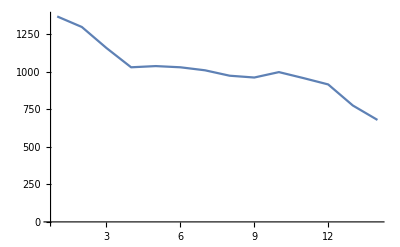

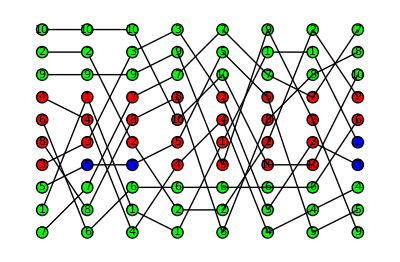

```mathematica
grPTbl=Table[DrawQBPlacementGlobal[BPtbl[[i]]],{i,1,Length[BPtbl]}];
Manipulate[Graphics[grPTbl[[i]]],{i,1,Length[grPTbl],1}]
```

### multi pass

```mathematica
ImprovePlacement2[BP_,Nq_,Fsizes_,Qmax_,Mmax_,numPasses_,echo_]:=Module[{numSteps,numF,pass,dir,stepStart,stepStop,step,z,zp,SP,GP,FP,c,SPp,GPp,FPp,cp,SPf,GPf,FPf,cf,q,qi,z2,qi2,q2,s1p,z2p,s12p,k,k2,kp,k2p,dist,distSwap,BPnew,Y,costTot,reapRes,costTotTbl,Ytemp,BPtbl},

Y=ComputeArrangements[BP,Nq,Fsizes,Qmax,Mmax];
costTot=ComputeTotalCost[Y,Nq];
If[echo==True,Print["ImprovePlacement costTot: ",costTot]];
numSteps=Length[BP];
numF=Length[Fsizes];
BPnew=BP;
dir=1;

reapRes=Reap[
Sow[costTot,1];
Sow[BPnew,2];
For[pass=1,pass≤numPasses,pass++,
Print["pass: ",pass," dir: ",dir];
If[dir==1,stepStart=2,stepStart=numSteps-1];
If[dir==1,stepStop=numSteps,stepStop=1];

For[step=stepStart,If[dir==1,step≤stepStop,step≥stepStop],step+=dir,
(*storage information from previous step*)
Print[" step: ",step, " step-dir: ",step-dir];
{SPp,GPp,FPp,cp}=BPnew[[step-dir]];
If[dir==1,If[step<stepStop,{SPf,GPf,FPf,cf}=BPnew[[step+dir]]],If[step>stepStop,{SPf,GPf,FPf,cf}=BPnew[[step+dir]]]];

(*1. - swap idle qubits between idle zones to prevent crossings*)
For[z=1,z≤numF,z++,
{SP,GP,FP,c}=BPnew[[step]];

(*iterate over all idle qubits*)
For[qi=1,qi≤Length[FP[[z]]],qi++,
{SP,GP,FP,c}=BPnew[[step]];
q=FP[[z,qi]];
zp=cp[[q,2]];
s1p=cp[[q,1]];
If[step<Length[BP], {zf=cf[[q,2]],s1f=cf[[q,1]]}];
(*if q was not idle in previous step or if it was in the same zone, we do not try to swap q*)
If[s1p!="i" || zp== z,Continue[]];

(*iterate over all idle zone QB as possible swap partners*)
For[qi2=1,qi2≤Length[FP[[zp]]],qi2++,
q2=FP[[zp,qi2]];
If[q2==q,Continue[]];
z2p=cp[[q2,2]];
s12p=cp[[q2,1]];
If[step<Length[BP], {z2f=cf[[q2,2]],s12f=cf[[q2,1]]}];

(*q2 is not a swap partner if it was not idle in previous step AND if q and q2 are contained in the same idle zone in the previous step*)
If[z2p==zp && s12p=="i",Continue[]];
(*q2 is not a swap partner if it is not idle in next step AND if q and q2 are contained in the same idle zone in the next step*)
If[step<numSteps,If[z2f==zf && s12f=="i",Continue[]]];
BPnew[[step,4,{q,q2}]]={c[[q2]],c[[q]]};
BPnew[[step,3,z]]=BPnew[[step,3,z]] /.q->q2;
BPnew[[step,3,zp]]=BPnew[[step,3,zp]] /.q2->q;
{costTot,Y[[step]]}=UpdateStep[Y,step,numSteps,q,q2,costTot];
Sow[costTot,1];
Sow[BPnew,2];
Break[];
];
];
];

(*2. - swap idle qubits within idle zones to minimize swaps*)
For[z=1,z≤numF,z++,
{SP,GP,FP,c}=BPnew[[step]];

For[qi=1,qi≤Length[FP[[z]]],qi++,
{SP,GP,FP,c}=BPnew[[step]];
q=FP[[z,qi]];
k=c[[q,3]];
zp=cp[[q,2]];
s1p=cp[[q,1]];
kp=cp[[q,3]];

(*if q was not idle in previous step or if it was not contained in the same idle zone, do not try to swap q*)
If[s1p!="i" || zp!= z,Continue[]];

(*iterate over all QB in same idle zone as possible swap partners*)
For[qi2=1,qi2≤Length[FP[[z]]],qi2++,
If[qi==qi2,Continue[]];
q2=FP[[z,qi2]];
If[q2==q,Continue[]];

s12p=cp[[q2,1]];
z2p=cp[[q2,2]];
(*if q2 was not idle in previous step or if it was stored in a different zone, do not swap*)
If[s12p!="i" || z2p≠z,Continue[]];
k2=c[[q2,3]];
k2p=cp[[q2,3]];

dist=(k-kp)^2+(k2-k2p)^2;
distSwap=(k-k2p)^2+(k2-kp)^2;

If[echo==True,Print[" candidates - f: ",z," fprev: ",zp," f2prev: ",z2p, " q: ",q," q2: ",q2]];
If[!(distSwap<dist),Continue[]];
If[echo==True,Print["  swap found - dist: ",dist," distSwap: ",distSwap]];
BPnew[[step,4,q]]=c[[q2]];
BPnew[[step,4,q2]]=c[[q]];
BPnew[[step,3,z,{qi,qi2}]]={q2,q};
{costTot,Y[[step]]}=UpdateStep[Y,step,numSteps,q,q2,costTot];
Sow[costTot,1];
Sow[BPnew,2];
Break[];
];
];
];

(*3. - swap entire processing zones to minimize swaps*)
For[z=1,z≤Mmax,z++,
{SP,GP,FP,c}=BPnew[[step]];
SPz=Flatten[SP[[z]],1];
For[z2=1,z2≤Mmax,z2++,
If[z==z2,Continue[]];
SPz2=Flatten[SP[[z2]],1];

dist=Sum[(Y[[step,SPz[[qi]]]]-Y[[step-dir,SPz[[qi]]]])^2+(Y[[step,SPz2[[qi]]]]-Y[[step-dir,SPz2[[qi]]]])^2,{qi,1,Length[SPz]}];
distSwap=Sum[(Y[[step,SPz2[[qi]]]]-Y[[step-dir,SPz[[qi]]]])^2+(Y[[step,SPz[[qi]]]]-Y[[step-dir,SPz2[[qi]]]])^2,{qi,1,Length[SPz]}];
If[distSwap<dist,{
BPnew[[step,1,{z,z2}]]=BPnew[[step,1,{z2,z}]];
For[qi=1,qi≤Qmax,qi++,{
BPnew[[step,4,SPz[[qi]],2]]=z2;
BPnew[[step,4,SPz2[[qi]],2]]=z;
{costTot,Y[[step]]}=UpdateStep[Y,step,numSteps,SPz[[qi]],SPz2[[qi]],costTot];
}];
Sow[costTot,1];
Sow[BPnew,2];
Break[];
}];
];
];

(*4. - swap qubits within processing zones to minimize swaps*)
For[z=1,z≤Mmax,z++,
{SP,GP,FP,c}=BPnew[[step]];
SPz=Flatten[SP[[z]],1];
For[qi=1,qi≤Length[SPz],qi++,
{SP,GP,FP,c}=BPnew[[step]];
SPz=Flatten[SP[[z]],1];
q=SPz[[qi]];
k=c[[q,3]];
zp=cp[[q,2]];
s1p=cp[[q,1]];
kp=cp[[q,3]];

(*if q was not same processing zone in previous step, do not try to swap q*)
If[s1p!="p" || zp!= z,Continue[]];

(*iterate over all QB in same idle zone as possible swap partners*)
For[qi2=1,qi2≤Length[SPz],qi2++,
If[qi==qi2,Continue[]];
q2=SPz[[qi2]];
If[q2==q,Continue[]];

s12p=cp[[q2,1]];
z2p=cp[[q2,2]];
(*if q2 was not in same processing zone in previous step, do not swap*)
If[s12p!="p" || z2p≠z,Continue[]];
k2=c[[q2,3]];
k2p=cp[[q2,3]];
dist=(k-kp)^2+(k2-k2p)^2;
distSwap=(k-k2p)^2+(k2-kp)^2;

If[echo==True,Print[" candidates - z: ",z," zprev: ",zp," z2prev: ",z2p, " q: ",q," q2: ",q2]];
If[!(distSwap<dist),Continue[]];
If[echo==True,Print["  swap found - dist: ",dist," distSwap: ",distSwap]];
BPnew[[step,4,q,3]]=k2;
BPnew[[step,4,q2,3]]=k;
{costTot,Y[[step]]}=UpdateStep[Y,step,numSteps,q,q2,costTot];
Sow[costTot,1];
Sow[BPnew,2];
Break[];
];
];
];
]; (*step loop*)
dir=-dir;
]; (*pass loop*)
]; (*Reap*)
costTotTbl=reapRes[[2,1]];
BPtbl=reapRes[[2,2]];
Ytemp=ComputeArrangements[BPnew,Nq,Fsizes,Qmax,Mmax];
If[echo==True,{
Print["ImprovePlacement costTot final:",costTot]; 
Print["Arrangement consistency: ",TrueQ[Ytemp==Y]];
}];

{BPnew,costTotTbl,BPtbl}
];
```

```mathematica
{BPnew,costTotTbl,BPtbl}=ImprovePlacement2[BP,Nq,Fsizes,Qmax,Mmax,4,False];
CellPrint[Show[ListPlot[costTotTbl,Joined->True]]];
grP=DrawQBPlacementGlobal[BPnew];
Graphics[grP]
```

pass: 1 dir: 1

step: 2 step-dir: 1

step: 3 step-dir: 2

step: 4 step-dir: 3

step: 5 step-dir: 4

step: 6 step-dir: 5

step: 7 step-dir: 6

step: 8 step-dir: 7

pass: 2 dir: -1

step: 7 step-dir: 8

step: 6 step-dir: 7

step: 5 step-dir: 6

step: 4 step-dir: 5

step: 3 step-dir: 4

step: 2 step-dir: 3

step: 1 step-dir: 2

pass: 3 dir: 1

step: 2 step-dir: 1

step: 3 step-dir: 2

step: 4 step-dir: 3

step: 5 step-dir: 4

step: 6 step-dir: 5

step: 7 step-dir: 6

step: 8 step-dir: 7

pass: 4 dir: -1

step: 7 step-dir: 8

step: 6 step-dir: 7

step: 5 step-dir: 6

step: 4 step-dir: 5

step: 3 step-dir: 4

step: 2 step-dir: 3

step: 1 step-dir: 2

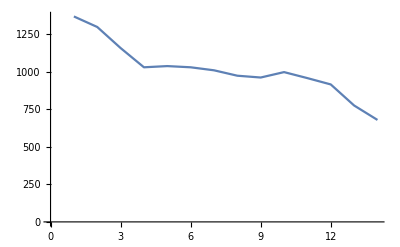

-Graphics-

## Tabu search

For efficiency reasons, the tabu search algorithm below does not operate on the BP data structure, i.e. it does not update these. It merely updates the arrangements tables, the zone tables and the s1 Tables (s1 status can change as idle qubits can be moved between idle zones and processing zones. s2 status does never change) 
For this reason, at the end of the tabu search, we have to rebuild the BP data structure, in particular the c tables storing the complete information about the storage
Arguments:
-BPold: input BP structure
-Fsizes: table of idle storage zone capacities
-Qmax: Processing zone capacity
-Mmax: Number of processing zones
-Nq: Number of qubits
-Y: arrangements, output of tabu search
-zonesTbl: table of zone indices for each step, output of tabu search
-s1Tbl: table of QB status "i" or "p", output of tabu search
-s2Tabl: table of QB status "a" or "i", not affected by tabu search
Output:
-BPnew: reconstructed BP structure

```mathematica
ReconstructBlocksFromArrangements[BPold_,Fsizes_,Qmax_,Mmax_,Nq_,Y_,zonesTbl_,s1Tbl_,s2Tbl_]:=Module[{BPnew,qbTbl,qbTblSort,step,SPnew,GP,FPnew,cNew,qi,q,cstep,FfillTbl,s1,s2,z,kiTbl,kpTbl,reapRes},
BPnew={};
qbTbl=Table[q,{q,1,Nq}];

reapRes=Reap[
For[step=1,step≤Length[Y],step++,
qbTblSort=qbTbl[[Ordering @ Y[[step]]]];
qbTblSort=Reverse[qbTblSort];
GP=BPold[[step,2]];
SPnew=Table[{{},{}},{m,1,Mmax}];
FPnew=Table[{},{f,1,Length[Fsizes]}];
cNew=Table[{},{q,1,Nq}];
kpTbl=Table[1,{m,1,Mmax}];
kiTbl=Table[1,{m,1,Length[Fsizes]}];
For[qi=1,qi≤Nq,qi++,
q=qbTblSort[[qi]];
s1=s1Tbl[[step,q]];
s2=s2Tbl[[step,q]];
z=zonesTbl[[step,q]];
If[s1=="i",{
cNew[[q]]={s1,z,kiTbl[[z]],s2};
kiTbl[[z]]++;
FPnew[[z]]=Append[FPnew[[z]],q];
},{
cNew[[q]]={s1,z,kpTbl[[z]],s2};
kpTbl[[z]]++;
If[s2=="a",SPnew[[z,1]]=Append[SPnew[[z,1]],q],SPnew[[z,2]]=Append[SPnew[[z,2]],q]];
}];
];
Sow[{SPnew,GP,FPnew,cNew}];
];
];
BPnew=reapRes[[2,1]];
BPnew
];
```

Tabu search algorithm
Arguments:
-BP: input BP structure, should be output from ImprovePlacement
-Fsizes: table of idle storage zone capacities
-Qmax: Processing zone capacity
-Mmax: Number of processing zones
-Nq: Number of qubits
-TSiterations: number of tabu search steps, e.g. 5000
-TSlen: Size of tabu list, e.g. 1000
-swapNumMax: maximum number of QB to cyclically swapped in one TS step (does not affect processing zone swaps)
-processingZoneSwapFraction: frequency of TS steps where we attempt to swap entire processing zones
-greadSpread: BOOL, indicates whether we expand successful swap to neighboring arrangements (currently still erronous)
-storeAllBestBP: BOOL, indicates whether to store and return all intermediate BP structures upon improvement for visualization, affects perfomance
-echo: BOOL, prints some debug output
Output:
-BPnew: reconstructed BP structure
-costProgressTbl: cost after swap for each TS step
-bestCostProgressTbl: best cost for each TS step
-YBest: final best arrangement
-numImprovements: number of TS steps where improvement was found
-tabuCtr: number of events where a swap was tabu
-noUpdateCtr: number of TS steps where no update was possible
-bestYAll: table of all intermediate arrangements where improvement was found
-bestCostUpdateAll: table of all 
-bestBPTblAll: table of all intermediate BP structures where improvement was found
-TStime: absolute runtime of TS main loop

```mathematica
ImprovePlacementTabuSearch[BP_,Fsizes_,Qmax_,Mmax_,Nq_,TSiterations_,TSlen_,swapNumMax_,processingZoneSwapFraction_,greedySpread_,storeAllBestBP_,echo_]:=Module[{numF,numProcessingQB,numIdleQB,processingQBratio,step,numSteps,QBTbl,c,SP,idleList,idlePools,processingList,processingPools,Y,zonesTbl,zonesList,s1Tbl,s1List,s2Tbl,s2List,qi,q,costTot,costBest,deltaCostBestLocal,TSlist,TSfill,
tabuCtr,noUpdateCtr,numImprovements,memberQqueries,numImprovementMultiSwaps,numImprovementTwoSwaps,numProcessingZoneSwaps,numImprovementProcessingZonesSwaps,
s2swap,s1swap,swapQBnum,processingZoneIndex,swapPool,swapPoolSize,numPossibleSwaps,subsets,rot,swapQBLists,swapQBListsSwapped,
deltaCostTbl,ord,ssi,stepp,deltaCost2,sqb,sqbi,
swapProcessingZones,processingZonesSwap,processingZone1,processingZone2,
poolSize,i,Yc,Yp,Yf,deltaCost,q1i,q1,q2i,q2,YTest,flag,YBestUpdate,YBest,zonesTblBestUpdate,zonesTblBest,s1TblBestUpdate,s1TblBest,s2TblBestUpdate,s2TblBest,costProgressTbl,bestCostProgressTbl,bestYAll,bestCostUpdateAll,bestBPTblAll,reapRes,TStime,BPnew},

numF=Length[Fsizes]; (*number of idle zones*)
numSteps=Length[BP];

idlePools={};
processingPools={};
zonesTbl={};
s1Tbl={};
s2Tbl={};
QBTbl=Table[q,{q,1,Nq}];

(*build data required data structures from BO: the pools of mutually swappable qubits and the tables containing the one indices and status values, and the arrangement tables containing the qubit positions in the register*)
For[step=1,step≤numSteps,step++,
SP=BP[[step,1]];
c=BP[[step,4]];
idleList={};
processingList=Table[{},Length[BP[[step,1]]]];
zonesList=Table[0,Nq];
s1List=Table[0,Nq];
s2List=Table[0,Nq];

For[q=1,q≤Nq,q++,
If[c[[q,4]]=="i",idleList=Append[idleList,q],{
processingList[[c[[q,2]]]]=Append[processingList[[c[[q,2]]]],q];
}];
zonesList[[q]]=c[[q,2]];
s1List[[q]]=c[[q,1]];
s2List[[q]]=c[[q,4]];
];
idlePools=Append[idlePools,idleList];
processingPools=Append[processingPools,processingList];
zonesTbl=Append[zonesTbl,zonesList];
s1Tbl=Append[s1Tbl,s1List];
s2Tbl=Append[s2Tbl,s2List];
];


(*compute total rearrangement cost from input arrangements*)
Y=ComputeArrangements[BP,Nq,Fsizes,Qmax,Mmax];
costTot=ComputeTotalCost[Y,Nq];

(* debug output*)
If[echo==True,{
Print["numF: ",numF, " numSteps: ",numSteps];
Print["Y: ",Y];
Print["zonesTbl: ",zonesTbl];
Print["s1Tbl: ",s1Tbl];
Print["s2Tbl: ",s2Tbl];
Print["processingPools: ",processingPools];
Print["idlePools: ",idlePools];
Print["START costTot:",costTot];
}];

(*Tabu search starts here*)
TSlist=Table[{},TSlen];
TSfill=1;
numImprovements=0;
tabuCtr=0;
noUpdateCtr=0;
memberQqueries=0;
numImprovementMultiSwaps=0;
numImprovementTwoSwaps=0;
numProcessingZoneSwaps=0;
numImprovementProcessingZonesSwaps=0;
costBest=costTot;
YBest=Y;
costProgressTbl=Table[{},TSiterations];
bestCostProgressTbl=Table[{},TSiterations];
YBest=Y;
zonesTblBest=zonesTbl;
s1TblBest=s1Tbl;
s2TblBest=s2Tbl;

TStime=AbsoluteTiming[{
reapRes=Reap[ (*reap sow best arrangements*)
For[i=1,i≤TSiterations,i++,

step=RandomInteger[{1,numSteps}];
If[i>processingZoneSwapFraction TSiterations,{
(*regular swap operation, pick single random qubit*)
swapProcessingZones=False;
q1=RandomInteger[{1,Nq}];
s1swap=s1Tbl[[step,q1]];
s2swap=s2Tbl[[step,q1]];
processingZoneIndex=zonesTbl[[step,q1]];
swapQBnum=RandomInteger[{2,swapNumMax}];
If[s2swap=="i",
{
swapPool=idlePools[[step]],
(*special case: we're to swap an idle QB stored in a processing zone, we can also swap it with active qubits within this zone*)
If[s1swap=="p" && swapQBnum==2,swapPool=Join[swapPool,processingPools[[step,processingZoneIndex]]]];
},{
If[processingZoneIndex > Mmax,{
Print["ERROR processingZoneIndex > Mmax, step: ",step," processingZoneIndex: ",processingZoneIndex," q1: ",q1," s1: ",s1Tbl[[step,q1]], " s2: ",s2Tbl[[step,q1]], " zone: ",zonesTbl[[step,q1]]];
Break[];
}];
swapPool=processingPools[[step,processingZoneIndex]];
}];
swapPool=DeleteCases[swapPool,q1];
swapPoolSize=Length[swapPool];
If[swapPoolSize<swapQBnum-1,swapQBnum=swapPoolSize];
subsets=Subsets[swapPool,{swapQBnum-1}];
numPossibleSwaps=Length[subsets];
rot=RandomInteger[{1,swapQBnum-1}];
swapQBLists=Table[Join[{q1},subsets[[ssi]]],{ssi,1,numPossibleSwaps}];
swapQBListsSwapped=Table[RotateLeft[swapQBLists[[ssi]],rot],{ssi,1,numPossibleSwaps}];
},{
(*swap two entire processing zones*)
swapProcessingZones=True;
numProcessingZoneSwaps++;
processingZonesSwap=RandomSample[Range[1,Mmax],2];
processingZone1=Select[QBTbl,(s1Tbl[[step,#]]=="p" && zonesTbl[[step,#]]==processingZonesSwap[[1]])&];
processingZone2=Select[QBTbl,(s1Tbl[[step,#]]=="p" && zonesTbl[[step,#]]==processingZonesSwap[[2]])&];
swapQBLists={Join[processingZone1,processingZone2]};
swapQBListsSwapped={Join[processingZone2,processingZone1]};
swapQBnum=Length[swapQBLists[[1]]];
numPossibleSwaps=1;
}];

(*initialize single iteration step*)
deltaCostBestLocal=1000000; (*very large value*)
Yc=Y[[step]];
If[step>1,Yp=Y[[step-1]],Yp=Table[0,Nq]];
If[step<numSteps,Yf=Y[[step+1]],Yf=Table[0,Nq]];

deltaCostTbl=Table[2(Yp[[swapQBLists[[ssi]]]]+Yf[[swapQBLists[[ssi]]]]).(Yc[[swapQBLists[[ssi]]]]-Yc[[swapQBListsSwapped[[ssi]]]]),{ssi,1,numPossibleSwaps}];

ord=Ordering[deltaCostTbl];
deltaCostTbl=deltaCostTbl[[ord]];
swapQBLists=swapQBLists[[ord]];
swapQBListsSwapped=swapQBListsSwapped[[ord]];

flag=False;

For[ssi=1,ssi<=numPossibleSwaps,ssi++,

YTest=Y;
YTest[[step,swapQBLists[[ssi]]]]=YTest[[step,swapQBListsSwapped[[ssi]]]];

memberQqueries++;
If[MemberQ[TSlist,YTest]==True,{
tabuCtr++;
Continue[];
}];

(*if not in tabu list, update best local cost, set update flag true and save swapped arrangement*)
flag=True;
deltaCostBestLocal=deltaCostTbl[[ssi]];

YBestUpdate=YTest;
zonesTblBestUpdate=zonesTbl;
s1TblBestUpdate=s1Tbl;
s2TblBestUpdate=s2Tbl;
zonesTblBestUpdate[[step,swapQBLists[[ssi]]]]=zonesTblBestUpdate[[step,swapQBListsSwapped[[ssi]]]];
s1TblBestUpdate[[step,swapQBLists[[ssi]]]]=s1TblBestUpdate[[step,swapQBListsSwapped[[ssi]]]];
(*NOTE: we do not swap on s2Tbl, as idle QB always remain idle QB*)
(*If[s2TblBestUpdate[[step,swapQBLists[[ssi]]]]!=s2TblBestUpdate[[step,swapQBListsSwapped[[ssi]]]],
Print["ERROR: s2Tbl changed under update, step: ",step, " swapList: ",swapQBLists[[ssi]], " swapList swapped: ",swapQBListsSwapped[[ssi]]," s2Tbl: ",s2TblBestUpdate[[step,swapQBLists[[ssi]]]]," s2 Tbl swapped:" ,s2TblBestUpdate[[step,swapQBListsSwapped[[ssi]]]]," zonesTbl: ",zonesTblBestUpdate[[step,swapQBLists[[ssi]]]]," zonesTbl swapped: ",zonesTblBestUpdate[[step,swapQBListsSwapped[[ssi]]]]," s1Tbl: ",s1TblBestUpdate[[step,swapQBLists[[ssi]]]]," s1Tbl swapped: ",s1TblBestUpdate[[step,swapQBListsSwapped[[ssi]]]]]];*)

(*try to update arrangement on steps left and right of selected step*)
If[greedySpread==False,Break[]];
stepp=step+1;
While[stepp≤numSteps,{
If[s2Tbl[[step,swapQBLists[[ssi]]]]!=s2Tbl[[stepp,swapQBLists[[ssi]]]] || zonesTbl[[step,swapQBLists[[ssi]]]]≠zonesTbl[[stepp,swapQBLists[[ssi]]]],Break[]];
Yc=YBestUpdate[[stepp]];
Yp=YBestUpdate[[stepp-1]];
If[stepp<numSteps,Yf=YBestUpdate[[stepp+1]],Yf=Table[0,Nq]];
deltaCost2=2(Yp[[swapQBLists[[ssi]]]]+Yf[[swapQBLists[[ssi]]]]).(Yc[[swapQBLists[[ssi]]]]-Yc[[swapQBListsSwapped[[ssi]]]]);
If[deltaCost2<0,{
deltaCostBestLocal+=deltaCost2;
YBestUpdate[[stepp,swapQBLists[[ssi]]]]=YBestUpdate[[stepp,swapQBListsSwapped[[ssi]]]];
zonesTblBestUpdate[[stepp,swapQBLists[[ssi]]]]=zonesTblBestUpdate[[stepp,swapQBListsSwapped[[ssi]]]];
s1TblBestUpdate[[stepp,swapQBLists[[ssi]]]]=s1TblBestUpdate[[stepp,swapQBListsSwapped[[ssi]]]];
For[sqbi=1,sqbi≤Length[swapQBLists[[ssi]]],sqbi++,
sqb=swapQBLists[[ssi,sqbi]];
If[s1TblBestUpdate[[stepp,sqb]]=="i" && s2TblBestUpdate[[stepp,sqb]]=="a",Print["  ERROR in greedy expansion, step: ",step," stepp: ",stepp, " sqb: ",sqb]]; 
];
},stepp=numSteps];
stepp++;
}];

stepp=step-1;
While[stepp>1,{
If[s2Tbl[[step,swapQBLists[[ssi]]]]!=s2Tbl[[stepp,swapQBLists[[ssi]]]] || zonesTbl[[step,swapQBLists[[ssi]]]]≠zonesTbl[[stepp,swapQBLists[[ssi]]]],Break[]];
Yc=YBestUpdate[[stepp]];
Yp=YBestUpdate[[stepp-1]];
If[stepp<numSteps,Yf=YBestUpdate[[stepp+1]],Yf=Table[0,Nq]];
deltaCost2=2(Yp[[swapQBLists[[ssi]]]]+Yf[[swapQBLists[[ssi]]]]).(Yc[[swapQBLists[[ssi]]]]-Yc[[swapQBListsSwapped[[ssi]]]]);
If[deltaCost2<0,{
deltaCostBestLocal+=deltaCost2;
YBestUpdate[[stepp,swapQBLists[[ssi]]]]=YBestUpdate[[stepp,swapQBListsSwapped[[ssi]]]];
zonesTblBestUpdate[[stepp,swapQBLists[[ssi]]]]=zonesTblBestUpdate[[stepp,swapQBListsSwapped[[ssi]]]];
s1TblBestUpdate[[stepp,swapQBLists[[ssi]]]]=s1TblBestUpdate[[stepp,swapQBListsSwapped[[ssi]]]];
For[sqbi=1,sqbi≤Length[swapQBLists[[ssi]]],sqbi++,
sqb=swapQBLists[[ssi,sqbi]];
If[s1TblBestUpdate[[stepp,sqb]]=="i" && s2TblBestUpdate[[stepp,sqb]]=="a",Print["  ERROR in greedy expansion, step: ",step," stepp: ",stepp, " sqb: ",sqb," swaptbl: ",swapQBLists[[ssi]]," s2tbl: ",s2Tbl[[step,swapQBLists[[ssi]]]]," s2tbl 2: ",s2Tbl[[step,swapQBLists[[ssi]]]]]]; 
];
},stepp=1];
stepp--;
}];

Break[];
];

If[flag==False,noUpdateCtr++];
If[flag==True,{
TSlist[[TSfill]]=YBestUpdate;
TSfill++;
If[TSfill>TSlen,TSfill=1];

(*update best values*)
Y=YBestUpdate;
zonesTbl=zonesTblBestUpdate;
s1Tbl=s1TblBestUpdate;
s2Tbl=s2TblBestUpdate;

costTot+=deltaCostBestLocal;
If[costTot<costBest,{
costBest=costTot;
YBest=YBestUpdate;
zonesTblBest=zonesTblBestUpdate;
s1TblBest=s1TblBestUpdate;
s2TblBest=s2TblBestUpdate;
numImprovements++;
Sow[YBest,1];
Sow[costBest,2];
If[storeAllBestBP==True,{
BPnew=ReconstructBlocksFromArrangements[BP,Fsizes,Qmax,Mmax,Nq,YBest,zonesTblBest,s1TblBest,s2TblBest];
Sow[BPnew,3];
}];

If[swapProcessingZones==False,
If[swapQBnum>2,numImprovementMultiSwaps++,numImprovementTwoSwaps++]];
If[swapProcessingZones==True,numImprovementProcessingZonesSwaps++];
},{
deltaCostBestLocal=0;
}];
}];
costProgressTbl[[i]]={i,costTot};
bestCostProgressTbl[[i]]={i,costBest};
];
];
}];

If[numImprovements==0,{
BPnew=BP;
bestCostUpdateAll={costBest};
If[echo==True,Print["NO IMPROVEMENT!!!"]];
},{
TStime=TStime[[1]];
bestYAll=reapRes[[2,1]];
bestCostUpdateAll=reapRes[[2,2]];
bestBPTblAll=If[storeAllBestBP==True,reapRes[[2,3]],{}];
BPnew=ReconstructBlocksFromArrangements[BP,Fsizes,Qmax,Mmax,Nq,YBest,zonesTblBest,s1TblBest,s2TblBest];
Ytemp2=ComputeArrangements[BPnew,Nq,Fsizes,Qmax,Mmax];
costTotBest2=ComputeTotalCost[Ytemp2,Nq];
If[Ytemp2≠YBest,Print["ERROR: Y table inconsistency"]];
}];

If[echo==True,{
Print["Final best cost: ",costBest];
Print["Final best cost 2: ",costTotBest2];
Print["Number of improvements: ",numImprovements];
Print["MemberQ queries: ",memberQqueries];
Print["numImprovementTwoSwaps: ",numImprovementTwoSwaps];
Print["numImprovementMultiSwaps: ",numImprovementMultiSwaps];
Print["numProcessingZoneSwaps: ",numProcessingZoneSwaps];
Print["numImprovementProcessingZonesSwaps: ",numImprovementProcessingZonesSwaps];
}];

{BPnew,costProgressTbl,bestCostProgressTbl,YBest,numImprovements,tabuCtr,noUpdateCtr,bestYAll,bestCostUpdateAll,bestBPTblAll,TStime}
];
```

## Alternating optimization

OptimizeArrangements performs a sequential optimization, doing a deterministic optimization and a tabu search in each step

```mathematica
OptimizeArrangements[BP_,Nq_,Fsizes_,Qmax_,Mmax_,numOptimizationSteps_,TSiterations_,TSlen_,echo_,visualOutput_]:=Module[{BPnew,totalBestCostTbl,costTotBest,BPbest,grPbest,grPtbl,Ytemp,costTotInitial,optimizationStep,costTotTbl,costProgressTbl,bestCostProgressTbl,YBest,bestYAll,bestCostUpdateAll,bestBPTblAll,numImprovements,tabuCtr,noUpdateCtr,TStime,BPnewTbl},

BPnew=BP;
totalBestCostTbl=Table[{},2 numOptimizationSteps];
grPtbl=Table[{},2 numOptimizationSteps];
grPbest={};
Ytemp=ComputeArrangements[BPnew,Nq,Fsizes,Qmax,Mmax];
costTotInitial=ComputeTotalCost[Ytemp,Nq];
If[echo==True,Print["INITIAL COST: ",costTotInitial]];
costTotBest=10^9;

For[optimizationStep=1,optimizationStep<=numOptimizationSteps,optimizationStep++,

If[echo==True,Print["optimizationStep: ",optimizationStep]];

{BPnew,costTotTbl,BPnewTbl}=ImprovePlacement[BPnew,Nq,Fsizes,Qmax,Mmax,False];
If[echo==True,Print["   deterministic improvement FINAL BEST COST: ",Last[costTotTbl]]];
If[visualOutput==True,{
totalBestCostTbl[[2 optimizationStep-1]]=costTotTbl;
grPtbl[[2 optimizationStep-1]]=Table[Graphics[DrawQBPlacementGlobal[BPnewTbl[[i]]]],{i,1,Length[BPnewTbl]}]
}];

{BPnew,costProgressTbl,bestCostProgressTbl,YBest,numImprovements,tabuCtr,noUpdateCtr,bestYAll,bestCostUpdateAll,bestBPTblAll,TStime}=ImprovePlacementTabuSearch[BPnew,Fsizes,Qmax,Mmax,Nq,TSiterations,TSlen,3,0,False,visualOutput,False];
If[echo==True,{
Print["   tabu search FINAL BEST COST: ",Last[bestCostUpdateAll], " numImprovements: ",numImprovements, " tabuCtr: ",tabuCtr," noUpdateCtr: ",noUpdateCtr];
CellPrint[Show[ListPlot[{costProgressTbl,bestCostProgressTbl},Joined->True,PlotRange->All]]]
}];

If[visualOutput==True,{
totalBestCostTbl[[2 optimizationStep]]=bestCostUpdateAll;
grPtbl[[2 optimizationStep]]=Table[Graphics[DrawQBPlacementGlobal[bestBPTblAll[[i]]]],{i,1,Length[bestBPTblAll]}]
}];

If[Last[bestCostUpdateAll]<costTotBest,{
costTotBest=Last[bestCostUpdateAll];
If[visualOutput==True,{
BPbest=Last[bestBPTblAll];
grPbest=Graphics[DrawQBPlacementGlobal[BPbest]];
}];
}];
];
grPtbl=Flatten[grPtbl,1];
totalBestCostTbl=Flatten[totalBestCostTbl,1];
{BPbest,grPbest,costTotBest,grPtbl,totalBestCostTbl,costTotInitial}
];
```

## Test section : Multiple processing zones

### Random circuit, aggregate, improve

{{1,{2,6}},{2,{13,14}},{3,{7,23}},{4,{4,11}},{5,{7,24}},{6,{22,23}},{7,{1,20}},{8,{1,24}},{9,{2,24}},{10,{1,9}},{11,{1,18}},{12,{8,10}},{13,{4,14}},{14,{14,23}},{15,{2,14}},{16,{6,18}},{17,{15,17}},{18,{3,22}},{19,{11,13}},{20,{3,19}},{21,{11,12}},{22,{13,19}},{23,{3,4}},{24,{14,24}},{25,{9,14}},{26,{1,13}},{27,{4,23}},{28,{6,21}},{29,{7,9}},{30,{6,25}},{31,{2,18}},{32,{14,15}},{33,{12,15}},{34,{3,13}},{35,{8,10}},{36,{9,25}},{37,{2,21}},{38,{7,21}},{39,{3,5}},{40,{2,20}},{41,{2,9}},{42,{6,9}},{43,{12,18}},{44,{11,17}},{45,{15,24}},{46,{12,17}},{47,{2,9}},{48,{4,11}},{49,{1,12}},{50,{14,19}}}

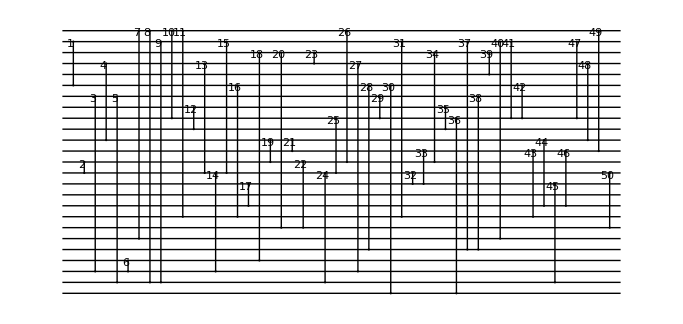

{{{1,{2,6}},{2,{13,14}},{3,{7,23}},{4,{4,11}},{7,{1,20}},{12,{8,10}},{17,{15,17}}},{{5,{7,24}},{6,{22,23}},{13,{4,14}},{19,{11,13}},{35,{8,10}}},{{8,{1,24}},{14,{14,23}},{18,{3,22}},{21,{11,12}}},{{9,{2,24}},{10,{1,9}},{20,{3,19}},{44,{11,17}}},{{11,{1,18}},{15,{2,14}},{22,{13,19}},{23,{3,4}}},{{16,{6,18}},{24,{14,24}},{26,{1,13}},{27,{4,23}}},{{25,{9,14}},{28,{6,21}},{31,{2,18}},{34,{3,13}},{48,{4,11}}},{{29,{7,9}},{30,{6,25}},{32,{14,15}},{37,{2,21}},{39,{3,5}}},{{33,{12,15}},{36,{9,25}},{38,{7,21}},{40,{2,20}},{50,{14,19}}},{{41,{2,9}},{43,{12,18}},{45,{15,24}}},{{42,{6,9}},{46,{12,17}}},{{47,{2,9}},{49,{1,12}}}}

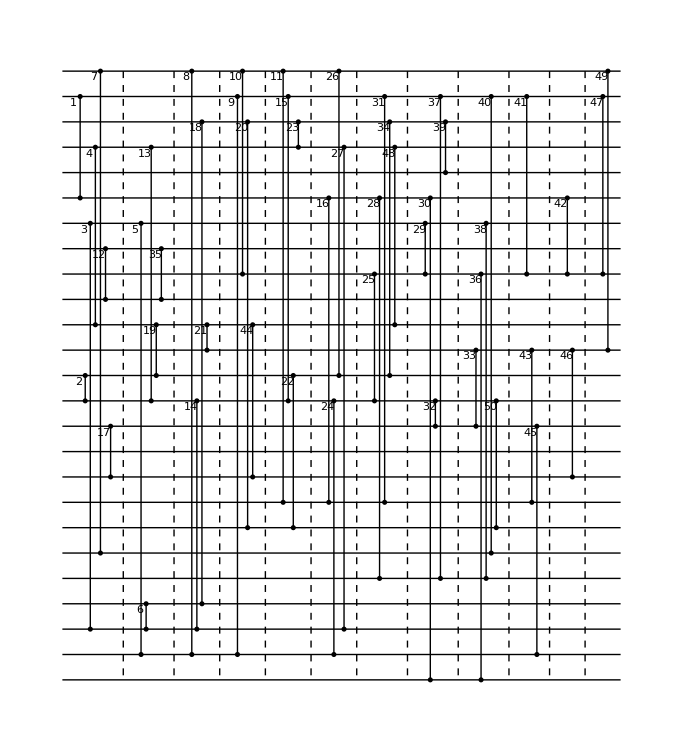

```mathematica
Nq=25;
Dg=50;
circ=randomCircuit[Nq,Dg]
cg=DrawCircuit[Nq,circ];
Graphics[cg]
layeredCirc=LayerCircuit[Nq,circ]
cg=DrawLayeredCircuit[Nq,layeredCirc];
Graphics[cg]
```

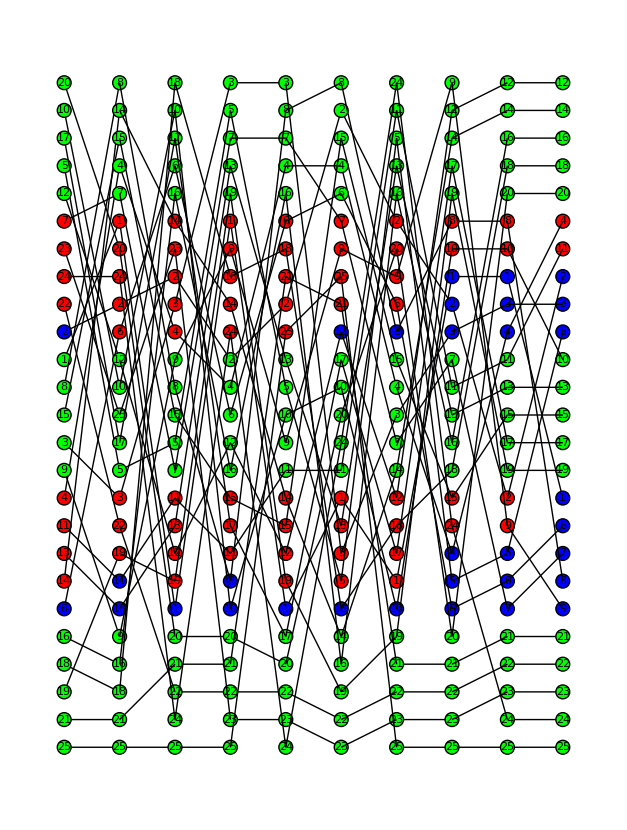

```mathematica
Fsizes={5,5,5};
Qmax=5;
Mmax=2;
BP=BlockProcessCircuit[circ,Nq,Fsizes,Qmax,Mmax];
(*PrintBP[BP];*)
grPraw=DrawQBPlacementGlobal[BP];
Graphics[grPraw]
```

```mathematica
{BPnew,costTotDetTbl,BPtbl}=ImprovePlacement[BP,Nq,Fsizes,Qmax,Mmax,False];
CellPrint[Show[ListPlot[costTotDetTbl,Joined->True]]];
grP=DrawQBPlacementGlobal[BPnew];
Graphics[grP]
```

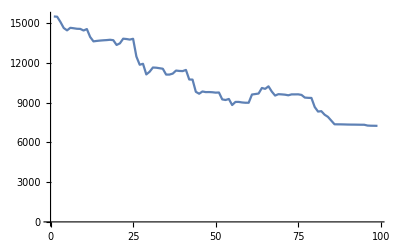

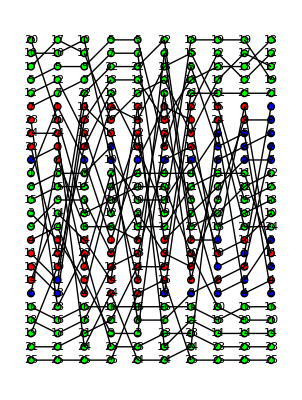

```mathematica
grPTbl=Table[DrawQBPlacementGlobal[BPtbl[[i]]],{i,1,Length[BPtbl]}];
Manipulate[Graphics[grPTbl[[i]]],{i,1,Length[grPTbl],1}]
```

Part::partd: Part specification grPTbl[[97]] is longer than depth of object.

### tabu search

numF: 3 numSteps: 10

Y: {{-5,-4,-8,-10,2,-14,0,-6,-9,4,-11,1,-12,-13,-7,-15,3,-16,-17,5,-18,-3,-1,-2,-19},{0,-3,-10,-9,3,-4,1,-5,-7,4,-13,2,-14,-8,-6,-16,5,-17,-12,-1,-18,-11,-15,-2,-19},{-4,-12,-13,-14,3,-9,2,-5,-7,5,0,-2,-1,-10,-6,-15,4,-16,-3,-8,-17,1,-11,-18,-19},{-10,-5,-17,-6,5,-9,4,-3,-11,-4,-2,-8,2,-13,0,-15,-1,-12,1,-7,-16,3,-18,-14,-19},{-4,-13,-17,-5,5,-10,4,-16,-8,-7,-9,-2,2,0,-1,-15,1,-11,-3,-6,-12,3,-18,-19,-14},{0,4,-2,-5,-3,1,-10,-16,-11,-7,-9,-14,-1,-18,3,-15,2,-4,-8,-6,-12,5,-17,-19,-13},{-1,-10,-7,-5,3,-13,-8,-14,-12,-4,-6,0,2,-16,4,-15,-2,-3,5,-11,1,-9,-17,-18,-19},{-12,-10,-14,-2,-3,-4,-6,-13,-7,-11,-5,4,3,-17,0,-16,2,-9,5,-15,1,-8,-18,-1,-19},{-11,0,-13,-14,-2,-3,-4,-12,-1,-10,-5,2,3,-17,-7,-15,4,-8,5,-16,1,-6,-18,-9,-19},{0,-12,-10,-13,-14,-2,-4,-3,-1,-8,-11,4,5,-17,-6,-15,3,-7,2,-16,1,-5,-18,-9,-19}}

zonesTbl: {{2,1,2,2,1,2,1,2,2,1,2,1,2,2,2,3,1,3,3,1,3,1,1,1,3},{1,1,2,2,1,1,1,2,2,1,2,1,2,2,2,3,1,3,2,1,3,2,3,1,3},{1,2,2,2,1,2,1,2,2,1,1,1,1,2,2,3,1,3,1,2,3,1,2,3,3},{2,2,3,2,1,2,1,1,2,1,1,2,1,2,1,3,1,2,1,2,3,1,3,2,3},{1,2,3,2,1,2,1,3,2,2,2,1,1,1,1,3,1,2,1,2,2,1,3,3,2},{1,1,1,2,1,1,2,3,2,2,2,2,1,3,1,3,1,1,2,2,2,1,3,3,2},{1,2,2,2,1,2,2,2,2,1,2,1,1,3,1,3,1,1,1,2,1,2,3,3,3},{2,2,2,1,1,1,2,2,2,2,2,1,1,3,1,3,1,2,1,3,1,2,3,1,3},{2,1,2,2,1,1,1,2,1,2,2,1,1,3,2,3,1,2,1,3,1,2,3,2,3},{1,2,2,2,2,1,1,1,1,2,2,1,1,3,2,3,1,2,1,3,1,2,3,2,3}}

s1Tbl: {{i,p,i,p,i,p,p,i,i,i,p,i,p,p,i,i,i,i,i,i,i,p,p,p,i},{p,p,p,i,i,p,i,i,i,i,p,i,p,i,i,i,i,i,p,p,i,p,i,p,i},{p,p,p,p,i,i,i,i,i,i,p,p,p,p,i,i,i,i,p,i,i,i,p,i,i},{p,i,i,i,i,i,i,p,p,p,p,i,i,p,p,i,p,p,i,i,i,i,i,p,i},{p,p,i,i,i,p,i,i,i,i,i,p,i,p,p,i,i,p,p,i,p,i,i,i,p},{p,i,p,i,p,i,p,i,p,i,i,p,p,i,i,i,i,p,i,i,p,i,i,i,p},{p,p,i,i,i,p,i,p,p,p,i,p,i,i,i,i,p,p,i,p,i,i,i,i,i},{p,p,p,p,p,p,i,p,i,p,i,i,i,i,p,i,i,i,i,i,i,i,i,p,i},{p,p,p,p,p,p,p,p,p,p,i,i,i,i,i,i,i,i,i,i,i,i,i,i,i},{p,p,p,p,p,p,p,p,p,i,p,i,i,i,i,i,i,i,i,i,i,i,i,i,i}}

s2Tbl: {{i,i,i,a,i,i,a,i,i,i,a,i,a,a,i,i,i,i,i,i,i,a,a,a,i},{a,a,a,i,i,a,i,i,i,i,i,i,i,i,i,i,i,i,a,a,i,a,i,a,i},{i,a,a,a,i,i,i,i,i,i,a,a,a,a,i,i,i,i,a,i,i,i,a,i,i},{a,i,i,i,i,i,i,i,a,i,a,i,i,a,a,i,a,a,i,i,i,i,i,a,i},{i,a,i,i,i,a,i,i,i,i,i,a,i,a,a,i,i,a,a,i,a,i,i,i,a},{a,i,a,i,a,i,a,i,a,i,i,i,a,i,i,i,i,i,i,i,a,i,i,i,a},{a,a,i,i,i,a,i,i,a,i,i,a,i,i,i,i,a,a,i,a,i,i,i,i,i},{i,i,i,i,i,i,i,a,i,a,i,i,i,i,a,i,i,i,i,i,i,i,i,a,i},{i,a,i,i,i,i,i,a,a,a,i,i,i,i,i,i,i,i,i,i,i,i,i,i,i},{i,i,i,a,i,i,i,i,i,i,a,i,i,i,i,i,i,i,i,i,i,i,i,i,i}}

processingPools: {{{7,22,23,24},{4,11,13,14}},{{1,2,6,20,24},{3,19,22}},{{11,12,13,19},{2,3,4,14,23}},{{11,15,17},{1,9,14,18,24}},{{12,14,15,19},{2,6,18,21,25}},{{1,3,5,13},{7,9,21,25}},{{1,12,17,18},{2,6,9,20}},{{15,24},{8,10}},{{2,9},{8,10}},{{},{4,11}}}

idlePools: {{1,2,3,5,6,8,9,10,12,15,16,17,18,19,20,21,25},{4,5,7,8,9,10,11,12,13,14,15,16,17,18,21,23,25},{1,5,6,7,8,9,10,15,16,17,18,20,21,22,24,25},{2,3,4,5,6,7,8,10,12,13,16,19,20,21,22,23,25},{1,3,4,5,7,8,9,10,11,13,16,17,20,22,23,24},{2,4,6,8,10,11,12,14,15,16,17,18,19,20,22,23,24},{3,4,5,7,8,10,11,13,14,15,16,19,21,22,23,24,25},{1,2,3,4,5,6,7,9,11,12,13,14,16,17,18,19,20,21,22,23,25},{1,3,4,5,6,7,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25},{1,2,3,5,6,7,8,9,10,12,13,14,15,16,17,18,19,20,21,22,23,24,25}}

START costTot:7242

Final best cost: 1660

Final best cost 2: 1660

Number of improvements: 216

MemberQ queries: 5014

numImprovementTwoSwaps: 113

numImprovementMultiSwaps: 103

numProcessingZoneSwaps: 0

numImprovementProcessingZonesSwaps: 0

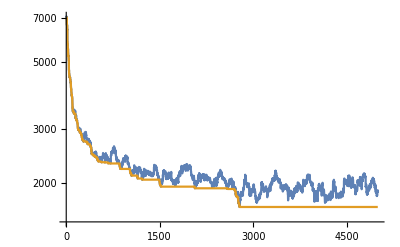

YBest: {{-7,-5,-8,-12,5,-1,0,-6,-17,4,-14,2,-10,-11,-9,-15,3,-16,-13,1,-19,-4,-3,-2,-18},{-3,-4,-11,-13,5,-2,1,-7,-16,4,-9,2,-5,-14,-6,-17,3,-15,-12,0,-19,-10,-8,-1,-18},{-8,-10,-12,-13,4,-5,2,-9,-15,5,-3,0,-1,-11,1,-19,3,-16,-4,-2,-18,-6,-14,-7,-17},{-10,-8,-6,-15,5,-7,-5,-9,-14,4,-1,1,3,-12,-2,-19,0,-13,-3,-4,-17,2,-18,-11,-16},{-6,-10,-4,-17,2,-12,-7,-15,-16,4,-5,-2,1,-3,0,-18,3,-11,-1,-8,-14,5,-19,-9,-13},{-3,-9,-4,-15,-2,-16,-11,-17,-14,1,-7,-1,0,-5,2,-19,4,-8,3,-10,-12,5,-18,-6,-13},{0,-12,-6,-15,2,-14,-13,-17,-10,-5,-8,-2,3,-7,1,-18,-1,-3,4,-11,-9,5,-19,-4,-16},{2,-8,-7,-14,1,-16,-15,-13,-5,-11,-6,-3,3,-9,0,-19,-2,-4,4,-12,-10,5,-17,-1,-18},{3,-4,-9,-11,0,-18,-15,-13,-3,-10,-8,-2,2,-7,1,-19,-5,-6,5,-12,-14,4,-17,-1,-16},{2,-7,-8,-11,1,-19,-14,-12,-2,-9,-10,-4,3,-6,0,-18,-3,-5,5,-13,-16,4,-17,-1,-15}}

final best cost: {5000,1660}

tabu ctr: 125

no update ctr: 111

TS time: 2.22974

```mathematica
{BPnew2,costProgressTbl,bestCostProgressTbl,YBest,numImprovements,tabuCtr,noUpdateCtr,bestYAll,bestCostUpdateAll,bestBPTblAll,TStime}=ImprovePlacementTabuSearch[BPnew,Fsizes,Qmax,Mmax,Nq,5000,1000,3,0,False,True,True];
ListLogPlot[{costProgressTbl,bestCostProgressTbl},Joined->True,PlotRange->All]
Print[" YBest: ",YBest]
Print["final best cost: ",Last[bestCostProgressTbl]]
Print["tabu ctr: ",tabuCtr]
Print["no update ctr: ",noUpdateCtr]
Print["TS time: ",TStime]
```

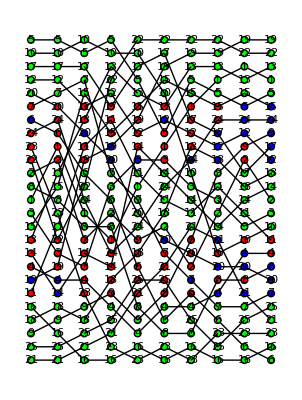

```mathematica
grP=DrawQBPlacementGlobal[BPnew2];
Graphics[grP]
```

```mathematica
grPtbl2=Table[Graphics[DrawQBPlacementGlobal[bestBPTblAll[[i]]]],{i,1,Length[bestBPTblAll]}];
```

```mathematica
grPtblBoth=Join[grPTbl,grPtbl2];
costPlotTbl=Join[costTotDetTbl,bestCostUpdateAll];
Manipulate[GraphicsRow[{Graphics[grPtblBoth[[i]]],Show[ListPlot[costPlotTbl,Joined->True,AspectRatio->1,Frame->True, FrameLabel->{Style["Update",16],Style["Swap cost",16]}],Graphics[Arrow[{{i,16000},{i,costPlotTbl[[i]]}}]]]},50,ImageSize->1000],{i,1,Length[grPtblBoth],1}]
```

Part::partd: Part specification grPtblBoth[[48]]
     is longer than depth of object.

ListPlot::lpn: costPlotTbl is not a list of numbers or pairs of numbers.

Part::partd: Part specification costPlotTbl[[48]]
     is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in 
    Show[ListPlot[costPlotTbl, Joined -> True, AspectRatio -> 1, 
      Frame -> True, FrameLabel -> {Update, Swap cost}], -Graphics-].

Part::partd: Part specification grPtblBoth[[240]]
     is longer than depth of object.

ListPlot::lpn: costPlotTbl is not a list of numbers or pairs of numbers.

Part::partd: Part specification costPlotTbl[[240]]
     is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in 
    Show[ListPlot[costPlotTbl, Joined -> True, AspectRatio -> 1, 
      Frame -> True, FrameLabel -> {Update, Swap cost}], -Graphics-].

Part::partd: Part specification grPtblBoth[[240]]
     is longer than depth of object.

ListPlot::lpn: costPlotTbl is not a list of numbers or pairs of numbers.

Part::partd: Part specification costPlotTbl[[240]]
     is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in 
    Show[ListPlot[costPlotTbl, Joined -> True, AspectRatio -> 1, 
      Frame -> True, FrameLabel -> {Update, Swap cost}], -Graphics-].

### Performance of different runs on same circuit

```mathematica
LaunchKernels[4]
```

{KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

```mathematica
res=ParallelTable[ImprovePlacementTabuSearch[BPnew,Fsizes,Qmax,Mmax,Nq,5000,1000,3,0,True,False],{i,1,30}];
```

```mathematica
bestCostProgressTbls=res[[All,2]];
```

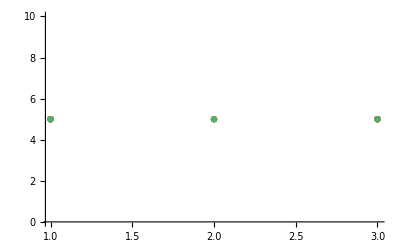

```mathematica
ListPlot[bestCostProgressTbls,PlotRange->All]
```

```mathematica
res=ParallelTable[ImprovePlacementTabuSearch[BPnew,Fsizes,Qmax,Mmax,Nq,5000,10,2,0,False,False],{i,1,30}];
```

```mathematica
bestCostProgressTbls=res[[All,2]];
```

```mathematica
ListPlot[bestCostProgressTbls,PlotRange->All]
```

-Graphics-

### alternating optimization

```mathematica
{BPbest,grPbest,costTotBest,grPtbl,totalBestCostTbl,costTotInitial}=OptimizeArrangements[BP,Nq,Fsizes,Qmax,Mmax,8,5000,100,True,True];
```

INITIAL COST: 15490

optimizationStep: 1

deterministic improvement FINAL BEST COST: 7242

tabu search FINAL BEST COST: 1734 numImprovements: 200 tabuCtr: 110 noUpdateCtr: 98

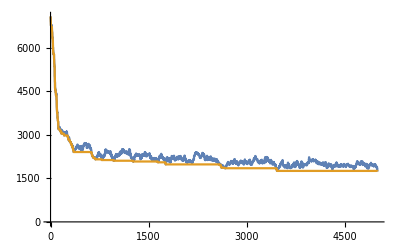

optimizationStep: 2

deterministic improvement FINAL BEST COST: 2854

tabu search FINAL BEST COST: 1738 numImprovements: 85 tabuCtr: 100 noUpdateCtr: 87

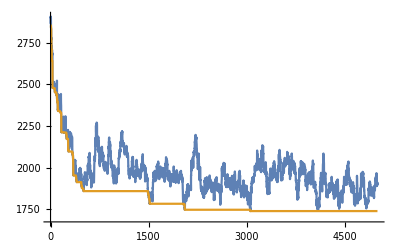

optimizationStep: 3

deterministic improvement FINAL BEST COST: 2000

tabu search FINAL BEST COST: 1698 numImprovements: 23 tabuCtr: 110 noUpdateCtr: 102

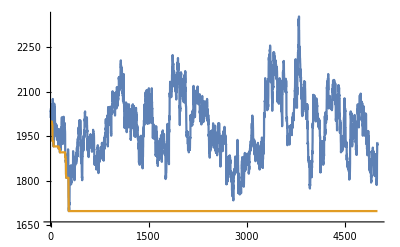

optimizationStep: 4

deterministic improvement FINAL BEST COST: 2324

tabu search FINAL BEST COST: 1754 numImprovements: 48 tabuCtr: 116 noUpdateCtr: 107

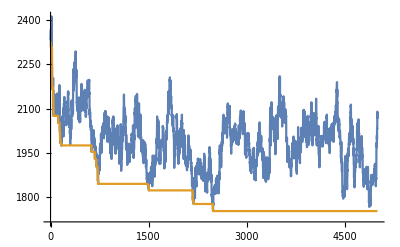

optimizationStep: 5

deterministic improvement FINAL BEST COST: 1918

tabu search FINAL BEST COST: 1720 numImprovements: 18 tabuCtr: 132 noUpdateCtr: 124

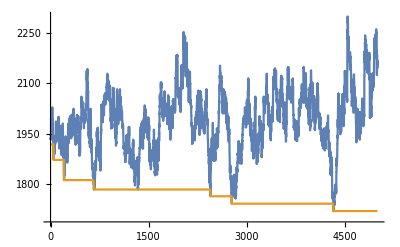

optimizationStep: 6

deterministic improvement FINAL BEST COST: 2922

tabu search FINAL BEST COST: 1734 numImprovements: 86 tabuCtr: 115 noUpdateCtr: 102

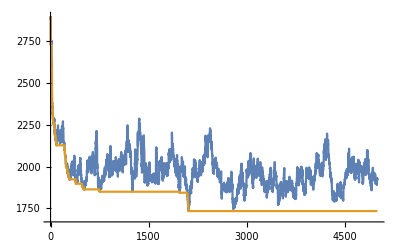

optimizationStep: 7

deterministic improvement FINAL BEST COST: 1890

tabu search FINAL BEST COST: 1634 numImprovements: 25 tabuCtr: 121 noUpdateCtr: 110

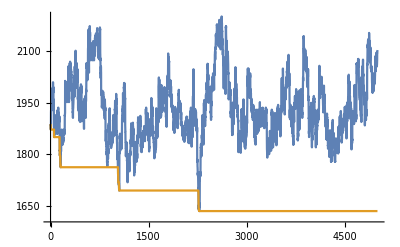

optimizationStep: 8

deterministic improvement FINAL BEST COST: 2604

tabu search FINAL BEST COST: 1600 numImprovements: 82 tabuCtr: 110 noUpdateCtr: 99

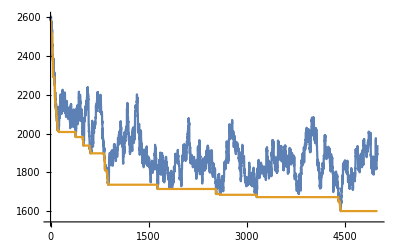

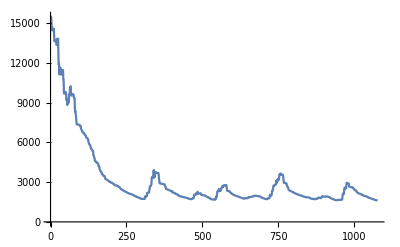

```mathematica
ListPlot[Flatten[totalBestCostTbl,1],Joined->True,PlotRange->All]
```

```mathematica
Manipulate[GraphicsRow[{Graphics[grPtbl[[i]]],Show[ListPlot[totalBestCostTbl,PlotRange->All,Joined->True,AspectRatio->1,Frame->True, FrameLabel->{Style["Update",16],Style["Swap cost",16]}],Graphics[Arrow[{{i,16000},{i,totalBestCostTbl[[i]]}}]]]},50,ImageSize->1000],{i,1,Length[grPtbl],1}]
```

Part::partd: Part specification grPtbl[[1]] is longer than depth of object.

ListPlot::lpn: totalBestCostTbl is not a list of numbers or pairs of numbers.

Part::partd: Part specification totalBestCostTbl[[1]]
     is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in 
    Show[ListPlot[totalBestCostTbl, PlotRange -> All, Joined -> True, 
      AspectRatio -> 1, Frame -> True, FrameLabel -> {Update, Swap cost}], 
     -Graphics-].

Part::partd: Part specification grPtbl[[1]] is longer than depth of object.

ListPlot::lpn: totalBestCostTbl is not a list of numbers or pairs of numbers.

Part::partd: Part specification totalBestCostTbl[[1]]
     is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in 
    Show[ListPlot[totalBestCostTbl, PlotRange -> All, Joined -> True, 
      AspectRatio -> 1, Frame -> True, FrameLabel -> {Update, Swap cost}], 
     -Graphics-].

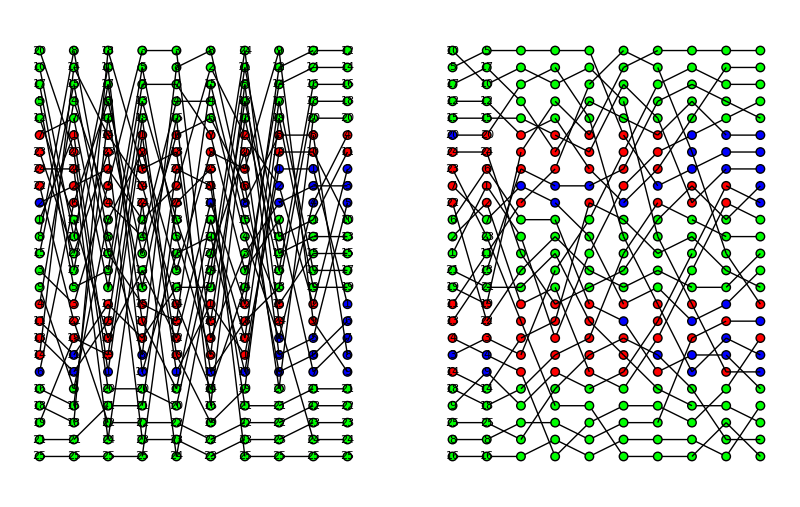

```mathematica
GraphicsRow[{First[grPtbl],grPbest}]
```

## Arranged circuit visualization

```mathematica
gatePitch=15;
QBPitch=15;
gapLength=25;

drawArrangedCircuit[BP_,Nq_]:=Module[{arrangementsTbl,res,step,x,xg,at,atn,q,y,col,c,GP,numG,g,q1,q2},

arrangementsTbl=Table[Table[yQBP[q,BP[[step,4]],BP[[step,1]],Fsizes,Qmax],{q,1,Nq}],{step,1,Length[BP]}];

x=0;
res=Reap[
For[step=1,step≤Length[arrangementsTbl],step++,
at=arrangementsTbl[[step]];
GP=BP[[step,2]];
c=BP[[step,4]];

numG=Max[Length /@ GP];

For[q=1,q≤Nq,q++,
col=If[c[[q,1]]=="p",If[c[[q,4]]=="a",Red,Blue],Black];
Sow[{col,Text[ToString[q],{x+QBPitch/2,QBPitch at[[q]]+QBPitch/3}]}];
Sow[{col,Line[{{x,QBPitch at[[q]]},{x+(numG+2) gatePitch,QBPitch at[[q]]}}]}];
];

For[pz=1,pz≤Length[GP],pz++,
xg=x+2 gatePitch;
For[g=1,g≤Length[GP[[pz]]],g++,
q1=GP[[pz,g,2,1]];
q2=GP[[pz,g,2,2]];
col=Black;
Sow[{col,Line[{{xg,QBPitch at[[q1]]},{xg , QBPitch at[[q2]]}}]}];
Sow[{col,Disk[{xg,QBPitch at[[q1]]},gatePitch/5]}];
Sow[{col,Disk[{xg,QBPitch at[[q2]]},gatePitch/5]}];
Sow[{col,FontSize->8,Text[ToString[GP[[pz,g,1]]],{xg-0.45 gatePitch,QBPitch Max[at[[q1]],at[[q2]]]-0.6 QBPitch}]}];
xg+=gatePitch;
];
];
x+= (numG+2)gatePitch;

If[step<Length[arrangementsTbl],{
atn=arrangementsTbl[[step+1]];
col=Black;
For[q=1,q≤Nq,q++,
Sow[{col,Line[{{x,QBPitch at[[q]]},{x+gapLength,QBPitch atn[[q]]}}]}];
];
x+=gapLength;
}];
];
];
res=res[[2,1]];
res
];
```

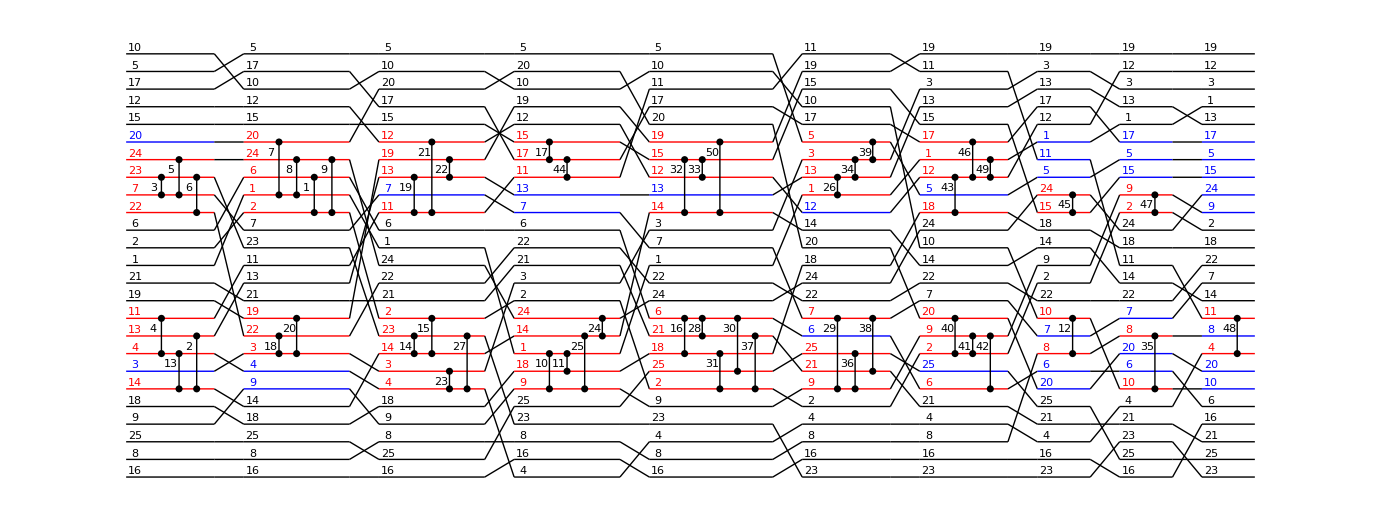

```mathematica
circArranged=drawArrangedCircuit[BPbest,Nq];
Graphics[circArranged]
```

## Optimization statistics

```mathematica
Nq=25;
Dg=50;
Fsizes={5,5,5};
Qmax=5;
Mmax=2;
circ=randomCircuit[Nq,Dg];
layeredCirc=LayerCircuit[Nq,circ];
BP=BlockProcessCircuit[circ,Nq,Fsizes,Qmax,Mmax];
```

```mathematica
t=AbsoluteTiming[{BPbest,grPbest,costTotBest,grPtbl,totalBestCostTbl,costTotInitial}=OptimizeArrangements[BP,Nq,Fsizes,Qmax,Mmax,10,1000,100,False,False]];
t[[1]]
```

5.7786

CloudConnect::vwarn: This version of Mathematica will no longer be supported for use with the Wolfram Cloud beginning Sun 1 Oct 2023. Please

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

```mathematica
LaunchKernels[8]
Needs["ErrorBarPlots`"]
SetSharedFunction[ParallelSow];
ParallelSow[expr_,slot_]:=Sow[expr,slot]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

### Independent runs, same random circuit, 5 stages, 500 TS iterations

```mathematica
nsamp=1000;
costInitialTbl=Table[0,nsamp];
costFinalTbl=Table[0,nsamp];
χTbl=Table[0,nsamp];
res=Reap[
ParallelDo[
{
{BPbest,grPbest,costTotBest,grPtbl,totalBestCostTbl,costTotInitial}=OptimizeArrangements[BP,Nq,Fsizes,Qmax,Mmax,5,500,100,False,False];
ParallelSow[N[costTotBest/costTotInitial],1];
ParallelSow[costTotBest,2];
},{i,nsamp}];
];
```

```mathematica
χtbl=res[[2,1]];
Export[NotebookDirectory[]<>"chiTblSameCircuit.dat",χtbl,"TSV"];
```

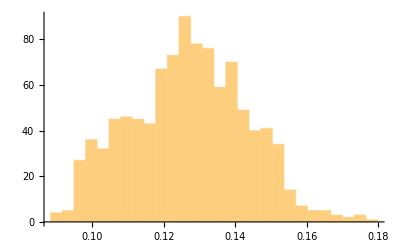

```mathematica
χtbl=Import[NotebookDirectory[]<>"chiTblSameCircuit.dat"];
χtbl=Flatten[χtbl];
Histogram[χtbl,{StandardDeviation[χtbl]/5}]
```

### Independent runs, different random circuits, 5 stages, 500 TS iterations

```mathematica
nsamp=1000;
costInitialTbl=Table[0,nsamp];
costFinalTbl=Table[0,nsamp];
χTbl=Table[0,nsamp];
res=Reap[
ParallelDo[
{
circ=randomCircuit[Nq,Dg];
layeredCirc=LayerCircuit[Nq,circ];
BP=BlockProcessCircuit[circ,Nq,Fsizes,Qmax,Mmax];
{BPbest,grPbest,costTotBest,grPtbl,totalBestCostTbl,costTotInitial}=OptimizeArrangements[BP,Nq,Fsizes,Qmax,Mmax,5,500,100,False,False];
ParallelSow[N[costTotBest/costTotInitial],1];
ParallelSow[costTotBest,2];
ParallelSow[costTotInitial,3];
},{i,nsamp}];
];
```

```mathematica
Export[NotebookDirectory[]<>"chiTblRandomCircuits.dat",Transpose[res[[2]]],"TSV"];
```

```mathematica
res=Import[NotebookDirectory[]<>"chiTblRandomCircuits.dat"];
χtbl=res[[All,1]];
cftbl=res[[All,2]];
citbl=res[[All,3]];
```

0.0208494

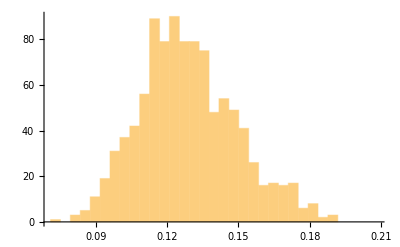

2000.78

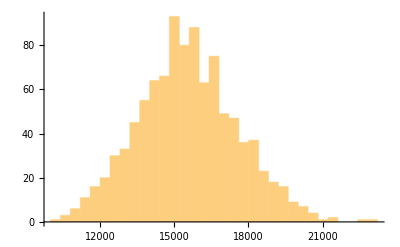

270.298

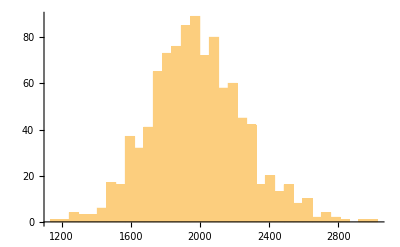

```mathematica
N[StandardDeviation[χtbl]]
Histogram[χtbl,{StandardDeviation[χtbl]/5}]
N[StandardDeviation[citbl]]
Histogram[citbl,{StandardDeviation[citbl]/5}]
N[StandardDeviation[cftbl]]
Histogram[cftbl,{StandardDeviation[cftbl]/5}]
```

### Different random circuits, variable TS iterations, 5 stages

```mathematica
nsamp=50;
optimizationStages=5;
TSIterationTbl={20,50,100,200,500,1000,2000};
χMeanTbl=Table[0,Length[TSIterationTbl]];
χStdTbl=Table[0,Length[TSIterationTbl]];

For[j=1,j≤Length[TSIterationTbl],j++,
costInitialTbl=Table[0,nsamp];
costFinalTbl=Table[0,nsamp];
χTbl=Table[0,nsamp];
res=Reap[
ParallelDo[
{
circ=randomCircuit[Nq,Dg];
layeredCirc=LayerCircuit[Nq,circ];
BP=BlockProcessCircuit[circ,Nq,Fsizes,Qmax,Mmax];
{BPbest,grPbest,costTotBest,grPtbl,totalBestCostTbl,costTotInitial}=OptimizeArrangements[BP,Nq,Fsizes,Qmax,Mmax,optimizationStages,TSIterationTbl[[j]],100,False,False];
ParallelSow[N[costTotBest/costTotInitial],1];
ParallelSow[costTotBest,2];
},{i,nsamp}];
];
χMeanTbl[[j]]=Mean[res[[2,1]]];
χStdTbl[[j]]=StandardDeviation[res[[2,1]]];
];

restbl=Transpose[{TSIterationTbl,χMeanTbl,χStdTbl}];
Export[NotebookDirectory[]<>"chiTblRandomCircuitsVariableTSiterations.dat",restbl,"TSV"];
```

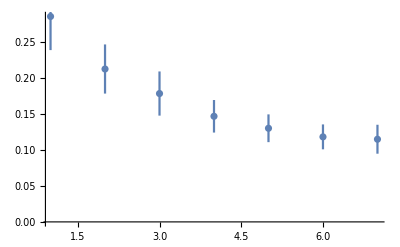

```mathematica
restbl=Import[NotebookDirectory[]<>"chiTblRandomCircuitsVariableTSiterations.dat"];
χPlotTbl=Table[{restbl[[i,2]],restbl[[i,3]]},{i,1,Length[restbl]}];
ErrorListPlot[χPlotTbl,PlotRange->All]
```

### Different random circuits, variable stages, 500 TS iterations

```mathematica
nsamp=50;
TSiterations=500;
OSTbl={1,2,5,10,20,50,100};
χMeanTbl=Table[0,Length[OSTbl]];
χStdTbl=Table[0,Length[OSTbl]];

For[j=1,j≤Length[OSTbl],j++,
Print["j:",j];
costInitialTbl=Table[0,nsamp];
costFinalTbl=Table[0,nsamp];
χTbl=Table[0,nsamp];
res=Reap[
ParallelDo[
{
circ=randomCircuit[Nq,Dg];
layeredCirc=LayerCircuit[Nq,circ];
BP=BlockProcessCircuit[circ,Nq,Fsizes,Qmax,Mmax];
{BPbest,grPbest,costTotBest,grPtbl,totalBestCostTbl,costTotInitial}=OptimizeArrangements[BP,Nq,Fsizes,Qmax,Mmax,OSTbl[[j]],TSiterations,100,False,False];
ParallelSow[N[costTotBest/costTotInitial],1];
ParallelSow[costTotBest,2];
},{i,nsamp}];
];
χMeanTbl[[j]]=Mean[res[[2,1]]];
χStdTbl[[j]]=StandardDeviation[res[[2,1]]];
];
restbl=Transpose[{OSTbl,χMeanTbl,χStdTbl}];
Export[NotebookDirectory[]<>"chiTblRandomCircuitsVariableOS.dat",restbl,"TSV"];
```

j:1

j:2

j:3

j:4

j:5

j:6

j:7

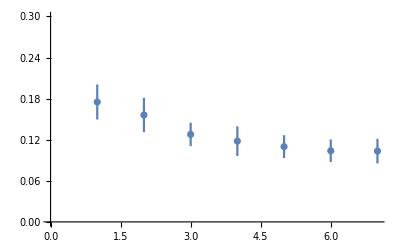

```mathematica
restbl=Import[NotebookDirectory[]<>"chiTblRandomCircuitsVariableOS.dat"];
χPlotTbl=Table[{restbl[[i,2]],restbl[[i,3]]},{i,1,Length[restbl]}];
elp1=ErrorListPlot[χPlotTbl,PlotRange->{0,0.3}]
```

### Different random circuits, variable stages, 200 TS iterations

```mathematica
nsamp=50;
TSiterations=200;
OSTbl={1,2,5,10,20,50,100};
χMeanTbl=Table[0,Length[OSTbl]];
χStdTbl=Table[0,Length[OSTbl]];

For[j=1,j≤Length[OSTbl],j++,
Print["j:",j];
costInitialTbl=Table[0,nsamp];
costFinalTbl=Table[0,nsamp];
χTbl=Table[0,nsamp];
res=Reap[
ParallelDo[
{
circ=randomCircuit[Nq,Dg];
layeredCirc=LayerCircuit[Nq,circ];
BP=BlockProcessCircuit[circ,Nq,Fsizes,Qmax,Mmax];
{BPbest,grPbest,costTotBest,grPtbl,totalBestCostTbl,costTotInitial}=OptimizeArrangements[BP,Nq,Fsizes,Qmax,Mmax,OSTbl[[j]],TSiterations,100,False,False];
ParallelSow[N[costTotBest/costTotInitial],1];
ParallelSow[costTotBest,2];
},{i,nsamp}];
];
χMeanTbl[[j]]=Mean[res[[2,1]]];
χStdTbl[[j]]=StandardDeviation[res[[2,1]]];
];
restbl=Transpose[{OSTbl,χMeanTbl,χStdTbl}];
Export[NotebookDirectory[]<>"chiTblRandomCircuitsVariableOS200.dat",restbl,"TSV"];
```

j:1

j:2

j:3

j:4

j:5

j:6

j:7

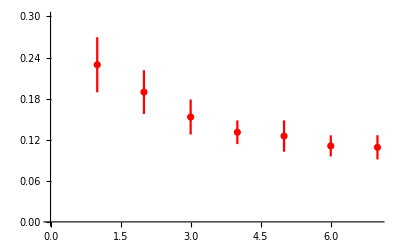

```mathematica
restbl=Import[NotebookDirectory[]<>"chiTblRandomCircuitsVariableOS200.dat"];
χPlotTbl=Table[{restbl[[i,2]],restbl[[i,3]]},{i,1,Length[restbl]}];
elp2=ErrorListPlot[χPlotTbl,PlotRange->{0,0.3},PlotStyle->RGBColor[1,0,0]]
```

### Different random circuits, variable stages, 50 TS iterations

```mathematica
nsamp=50;
TSiterations=50;
OSTbl={1,2,5,10,20,50,100};
χMeanTbl=Table[0,Length[OSTbl]];
χStdTbl=Table[0,Length[OSTbl]];

For[j=1,j≤Length[OSTbl],j++,
Print["j:",j];
costInitialTbl=Table[0,nsamp];
costFinalTbl=Table[0,nsamp];
χTbl=Table[0,nsamp];
res=Reap[
ParallelDo[
{
circ=randomCircuit[Nq,Dg];
layeredCirc=LayerCircuit[Nq,circ];
BP=BlockProcessCircuit[circ,Nq,Fsizes,Qmax,Mmax];
{BPbest,grPbest,costTotBest,grPtbl,totalBestCostTbl,costTotInitial}=OptimizeArrangements[BP,Nq,Fsizes,Qmax,Mmax,OSTbl[[j]],TSiterations,100,False,False];
ParallelSow[N[costTotBest/costTotInitial],1];
ParallelSow[costTotBest,2];
},{i,nsamp}];
];
χMeanTbl[[j]]=Mean[res[[2,1]]];
χStdTbl[[j]]=StandardDeviation[res[[2,1]]];
];
restbl=Transpose[{OSTbl,χMeanTbl,χStdTbl}];
Export[NotebookDirectory[]<>"chiTblRandomCircuitsVariableOS50.dat",restbl,"TSV"];
```

j:1

j:2

j:3

j:4

j:5

j:6

j:7

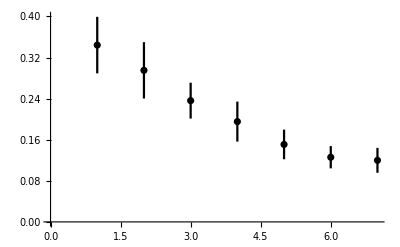

```mathematica
restbl=Import[NotebookDirectory[]<>"chiTblRandomCircuitsVariableOS50.dat"];
χPlotTbl=Table[{restbl[[i,2]],restbl[[i,3]]},{i,1,Length[restbl]}];
elp4=ErrorListPlot[χPlotTbl,PlotRange->{0,0.4},PlotStyle->RGBColor[0,0,0]]
```

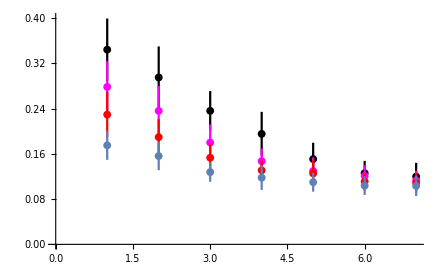

```mathematica
Show[elp4,elp3,elp2,elp1]
```

### Different random circuits,20 stages,100 TS iterations, variable TS list length

```mathematica
nsamp=50;
TSiterations=50;
optimizationStages=20;
TSlenTbl={1,10,50,100,500,1000};
χMeanTbl=Table[0,Length[TSlenTbl]];
χStdTbl=Table[0,Length[TSlenTbl]];

For[j=1,j≤Length[TSlenTbl],j++,
Print["j:",j];
costInitialTbl=Table[0,nsamp];
costFinalTbl=Table[0,nsamp];
χTbl=Table[0,nsamp];
res=Reap[
ParallelDo[
{
circ=randomCircuit[Nq,Dg];
layeredCirc=LayerCircuit[Nq,circ];
BP=BlockProcessCircuit[circ,Nq,Fsizes,Qmax,Mmax];
{BPbest,grPbest,costTotBest,grPtbl,totalBestCostTbl,costTotInitial}=OptimizeArrangements[BP,Nq,Fsizes,Qmax,Mmax,optimizationStages,TSiterations,TSlenTbl[[j]],False,False];
ParallelSow[N[costTotBest/costTotInitial],1];
ParallelSow[costTotBest,2];
},{i,nsamp}];
];
χMeanTbl[[j]]=Mean[res[[2,1]]];
χStdTbl[[j]]=StandardDeviation[res[[2,1]]];
];
restbl=Transpose[{TSlenTbl,χMeanTbl,χStdTbl}];
Export[NotebookDirectory[]<>"chiTblRandomCircuitsVariableTSlen.dat",restbl,"TSV"];
```

j:1

j:2

j:3

j:4

j:5

j:6

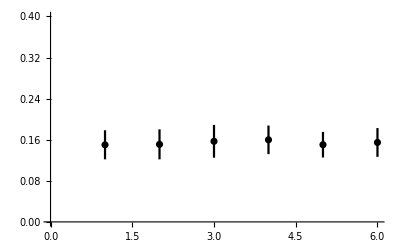

```mathematica
restbl=Import[NotebookDirectory[]<>"chiTblRandomCircuitsVariableTSlen.dat"];
χPlotTbl=Table[{restbl[[i,2]],restbl[[i,3]]},{i,1,Length[restbl]}];
elp4=ErrorListPlot[χPlotTbl,PlotRange->{0,0.4},PlotStyle->RGBColor[0,0,0]]
```